04

变分原理初步  哈密顿原理

拉格朗日力学相当成功，哈密顿力学似乎更为成功。

其实这两个力学形式在很大程度上将力学写成更为一般的形式（相比于牛顿力学），

以至于其他物理学科的发展也从中有所启发，有所借鉴，有所作为，有所成就。

其实，再往前走一步，就到了“定于一尊” —— 最小作用量原理 —— 的境界。

为再往前走一步，我们需要涉及到一些数学，现在就来个回顾或扫盲、科普先。

这些数学原理不但有助于学习分析力学，对今后学习经典场论乃至量子场论都会有所帮助

—— 如果你对物理的热情在学完本门课程还能 survive 的话。

设想在三维空间两个确定的点 A  和 B 之间画一条曲线。

这条曲线称为两点之间的一条路线。

现在，我们希望计算某一个物理量沿这条路线的线积分。

例如，如果这个物理量可以是沿着路线的距离的增量 ⅆs ，则

沿两点之间的一条路线所做的线积分 ∫_A^B ⅆs，就等于 A, B 间这条路线的总长度。

现在，有几条路线过同样的这两点的路线，沿不同路线的积分值当然会因路线改变而不同。

变分原理就要研究比较沿经过确定两点的不同路线的线积分大小，求出其极值路线。

比如，研究比较经过空间确定的两点的不同路线的长度大小，寻找最小值。

too easy, too trivial, sometimes naive, even low.  “图样图森破桑潭木乃伊，移门漏”

不就是连接两点的直线嘛。（但是，如果路线必须在指定的曲面上呢？——  有约束情况）

## § 4.1 变分

### § 4.1.1 N 维空间的路线及其变化的描述

为了要在分析力学中得到应用，我们感兴趣的是 N 维空间曲线。——  因为位形空间不限于三维（是 D 维）。

回顾多元微积分中计算线积分最为方便的方法 —— 将路线表示为参数方程。

为此，任意 N 维空间中的路线用一组参数方程，描述

x_k=x_k(β),        k=1,2,…,N                         描述 N 维空间曲线

还记得用参数方程描述空间曲线，对参量 β 有何要求？（单调）

假设在确定两个端点情况下，我们任意选择了一条路线计算线积分，并将这条路线称为预设路线（未变路线）。

这条路线 x_k(β) 由下列参数方程描述

x_k=x_k(β),        k=1,2,…,N

记两端点对应于参数方程的 β 值为： β_1 和  β_2

起点和终点的坐标为：

x_k^(1)=x_k(β_1),    x_k^(2)=x_k(β_2),     k=1,2,…, N

在定义了预设路线之后，再考虑经过相同起点和终点的另一些路线 —— 称为变化路线。

为了描述路线差别，引入一个标度变量 δa 和 N 个所谓 变形函数 η_k(β)，从而

变化路线记为 x_k(β,δa)，描述变换路线的参数方程为

x_k(β,δa)=x_k(β)+δa η_k(β)

其中变形函数 η_k(β) 可以是 β 的任意有限、可微函数，当然还需满足端点条件

η_k(β_1)=η_k(β_2)=0,     k=1,2,…, N

以保证变化路线与预设路线起始、终止于同样的两个端点。

这里标度参数（标度变量） δa 用于表征预设路线和变化路线的差别。

当 δa→0 时，只要变形函数 η_k(β) 是有限的，变化路线和预设路线重合。

这个标度参数对所有坐标 x_k相同（与 k 无关），并且对整条路线也相同（与 β 无关）。

未变路线和变化路线在不同坐标、不同位置时的差异，全部归并到变形函数 η_k(β) 中。

——  回顾函数极值的定义方法，比较两者之差异。

### § 4.1.2 坐标的变分

这里涉及的变分原理研究的是：

一个坐标变量的函数，

沿预设路线的线积分 和 沿变化路线的线积分 两者值差别。（当然，路线的变化是微小的）

为此，我们先来看坐标本身以及坐标对 β 的导数在变化路线 x_k(β,δa)=x_k(β)+η_k(β)δ a 和预设路线 x_k(β) 的差别

即，先来看坐标及其对参数 β 的导数的变分。

-Graphics-

上图描述了预设路线（未变路线，黑色）和两条 η_k 相同而 δa 不同的变化路线的第 k 个坐标 x_k(β)。

如前述，我们先看以下几个量。（都在相同的 β 值作比较。思考：为何不在不同 β 值上比较）因为我们要做积分 ∫...ⅆβ

变化路线的坐标和未变路线的坐标之差别  δx_k(β)  —— 称为坐标的变分

δx_k(β)=x_k(β,δa)-x_k(β)=δa η_k(β)          记得     x_k(β,δa)=x_k(β)+δa η_k(β)

坐标的变分如图紫色那段标注，显然 δx_k(β) 是 β 的函数，且满足：δx_k(β_1)=δx_k(β_2)=0

未变路线的坐标对 β 的导数

(ẋ)_k(β)≡(ⅆx_k(β))/ⅆβ    本章以顶标点表示对 β 求导（不同于前几章用它表示对时间的全导数）

变化路线的坐标对 β 的导数，记得变化路线的坐标  x_k(β,δa)=x_k(β)+δa η_k(β)

(ẋ)_k(β, δa)=(ⅆx_k(β, δa))/ⅆβ=(ẋ)_k(β)+ δa (η̇)_k(β)     记得标度变量 δa 与 β 和 k 都无关

变化路线的坐标对 β 的导数和未变路线坐标对 β 的导数之差  δ(ẋ)_k(β) ——   称为坐标对 β 的导数的变分

δ(ẋ)_k(β)=(ẋ)_k(β, δa)-(ẋ)_k(β)=δa (η̇)_k(β)=ⅆ/ⅆβ[δa η_k(β)]=ⅆ/ⅆβ[δx_k(β)]

从而有：

δ(ⅆx_k(β))/ⅆβ=ⅆ/ⅆβ[δx_k(β)]             简称为微分、变分可交换次序

思考：请用语言描述这个等式的含义。

坐标对 β 的导数在变化路线上的值与它在未变路线的值之差

等于变化路线上的坐标和未变路线的坐标之差对 β 的导数

以上等式，还可以写成

x_k(β, δa)=x_k(β)+δx_k(β),    (ẋ)_k(β, δa)=(ẋ)_k(β)+δ(ẋ)_k(β)=(ẋ)_k(β)+ⅆ/ⅆβ[δx_k(β)]=(ẋ)_k(β)+ⅆ/ⅆβ[δa η_k(β)]

其含义是：对每个给定的 β 值，变化路线上的值等于未变路线上的值加上相应的变分

### § 4.1.3 坐标的函数的变分

现在再来看坐标函数的变分，即函数在变化路线上的值与它在未变路线上的值之差。

函数 f(x,ẋ) 的变分定义为

函数在变化路线上的值与它在未变路线上的值之差。

Δf=f[x(β, δa), ẋ(β, δa)]-f[x(β), ẋ(β)]

记得 x(β, δa) 和  ẋ(β, δa)  分别表示 x 和 ẋ 在变化路线上的值，x(β), ẋ(β) 为在未变路线上的值

因为标度参量 δa 很小，若把 Δf 视为 δa 的函数，可以做 Taylor 展开（这里看到引入 δa 的意义）

(f[x(β, δa), ẋ(β, δa)]=f[x(β,h),ẋ(β,h)]_|)_(h=0)+[(∂f[x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa+1/(2!)[(∂^2 f[x(β,h),ẋ(β,h)])/(∂h^2)]_(h=0)(δa)^2+…

((比较函数的Taylor展开：f(x)=f(0)+1/(1!)f'(x)|)_(x=0) x+1/(2!)  f''(x)|)_(x=0) x^2+...

故： Δf=[(∂f[x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa+1/(2!)[(∂^2 f[x(β,h),ẋ(β,h)])/(∂h^2)]_(h=0)(δa)^2+…                           (‡)

一阶变分，Taylor 展开只取第一项，即为 δf,

δf=[(∂f[x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa                                                                                                                      (¶)

正如函数的一阶导数为 0 对应于极值点（驻值点），从 (‡) 式（Taylor 展开）可见，一阶变分为 0 也对应于变分的极值点，

从而，极值（驻值）可以用一阶变分为 0 作为条件来寻找（尽管这个条件上无法辨别极大、极小或拐点）。

驻值点：在那一点上可以驻扎下来（达到平衡）的点（尽管未必是稳定平衡）

一阶变分可以进一步化为

δf=[(∂f[x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa                     此即 式 (¶)
=(∑_(k=1))^N[(∂f(x,ẋ))/(∂x_k)(∂x_k(β,h))/(∂h)δa+(∂f(x,ẋ))/(∂(ẋ)_k)(∂OverDot[x_k](β,h))/(∂h)δa]      
                                        利用  {x_k(β,δa)=x_k(β)+_ δa η_k(β)
(ẋ)_k(β,δa)=(ẋ)_k(β)+δa_ (η̇)_k(β)        h≡δa
=(∑_(k=1))^N[(∂f(x,ẋ))/(∂x_k)η_k(β)δa+(∂f(x,ẋ))/(∂(ẋ)_k)(η̇)_k(β)δa]
δf=(∑_(k=1))^N[(∂f(x,ẋ))/(∂x_k)δx_k(β)+(∂f(x,ẋ))/(∂(ẋ)_k) δ(ẋ)_k(β)]

变分公式与微分公式相似：ⅆf=(∑_(k=1))^N[(∂f(x,ẋ))/(∂x_k)ⅆ x_k+(∂f(x,ẋ))/(∂(ẋ)_k)ⅆ(ẋ)_k]

其中，所有关于 f 的偏导数，均为先求偏导，再在未变路线（对应于 h=δa=0）上求值。

##### 如果函数 f 显含参数 β，即：f[β,x(β), ẋ(β)]，其变分如何？

记得变分是在给定参数 β_ 条件下，
函数在变化路线上的值与它
          在未变路线上的值之差。_
故：
Δf=_ f[β,x(β, δa), ẋ(β, δa)]-f[β,x(β), ẋ(β)]-Graphics-

因为 δa 很小，Δf 在 δa=0 邻域做 Taylor 展开，于是有

Δf=[(∂f[β,x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa+1/(2!)[(∂^2 f[β,x(β,h),ẋ(β,h)])/(∂h^2)]_(h=0)(δa)^2+…

考虑一阶变分，Taylor 展开只取第一项，即为δf,

δf=[(∂f[β,x(β,h),ẋ(β,h)])/(∂h)]_(h=0)δa 
=(∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)(∂x_k(β,h))/(∂h)δa+(∂f(β,x,ẋ))/(∂(ẋ)_k)(∂OverDot[x_k](β,h))/(∂h)δa]      
                                        利用  {x_k(β,δa)=x_k(β)+_ δa η_k(β)
((ẋ)_k(β,δa))_=(ẋ)_k(β)+δa (η̇)_k(β)          h≡δa
=(∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)η_k(β)δa+(∂f(β,x,ẋ))/(∂(ẋ)_k)(η̇)_k(β)δa]

可导得：

δf[β,x(β),ẋ(β)]=(∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)δx_k(β)+(∂f(β,x,ẋ))/(∂(ẋ)_k)δ(ẋ)_k(β)]

除了不出现    (∂f(β,x,ẋ))/(∂β) 项，变分公式与微分公式相似

当然，这里的条件是：β 作为空间曲线参数方程的参数。x, ẋ  都是 β 的函数

### § 4.1.4 函数的线积分的变分

沿着某条路线从 A 点到 B 点的线积分，基于参数方程计算最为简单。

函数f(β,x,ẋ) 沿某路线的线积分为（利用路线的参数方程计算线积分）

I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ        ——  这是沿预设（未变）路线的积分

如果积分沿变化路线进行，那么积分值依赖于：

标度参量 δa，未变路线 x_k(β)，还有变形函数 η_k(β),     k=1,2,…, N

这是因为变化路线由这几个因素共同决定。（变化路线是未变路线的微变，故与未变路线有关）

所以，积分值应该由这些因素共同决定

I(δa,[x],[η])=∫_β_1^β_2 f[β,x(β,δa),ẋ(β,δa)]ⅆβ    ——  沿变化路线的积分

除了标度参量 δa，上式方括号表示积分值决定于：坐标函数 x_k(β), 变形函数 η_k(β),。

所以这里的积分值是个泛函，是坐标函数和变形函数，即 x_k(β), η_k(β) ， 的函数，（是 函数的函数）

积分值 I(δa,[x],[η])  决定于这两个函数，x_k(β), η_k(β) ，在从 β_1 到 β_2 整个区间的值。

显然，沿预设路线（未变路线）的线积分可以改写成

I(0,[x],[η])=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ             即变化路线积分中取   δa=0

积分值的变分（沿两条路线积分之差）为

Δ I=I_(δa,[x],[η])-I(0,[x],[η])
=∫_β_1^β_2 f[β,x(β,δa),ẋ(β,δa)]ⅆβ-∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ
=∫_β_1^β_2 {f^[β,x(β,δa),ẋ(β,δa)]-f[β,x(β),ẋ(β)]}_函数的变分 ⅆβ     （意味着积分与变分可交换次序）
                           记得求导与变分也可交换次序
=∫_β_1^β_2 Δfⅆβ      要算线积分 I 的变分，需要被积函数的变分

至此我们应知道变分的三个性质：与微分、积分均可交换次序，求法类似于求微分

函数的变分怎么求？ ——   Taylor 展开

将 Δf的 Taylor展开式代入上式，并注意到 δa 与积分变量 β 无关，

Δ I={∫_β_1^β_2 [(∂f[β,x(β,h),ẋ(β,h)])/(∂h)]_(h=0)ⅆβ}δa+{∫_β_1^β_2 1/(2!)[(∂^2 f[β,x(β,h),ẋ(β,h)])/(∂h^2)]_(h=0)ⅆβ}(δa)^2+...

注意上式花括号中的值仅决定于未变路线（因为取的是 h=0 处的值）。保留到一阶项得

δI=∫_β_1^β_2 δfⅆβ

代入上一节的 δ f  表达式，

δf=(∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)δx_k(β)+(∂f(β,x,ẋ))/(∂(ẋ)_k)δ(ẋ)_k(β)]     （记得变分没有对参数 β 求偏导的那一项）

可得

δI=∫_β_1^β_2 (∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)δx_k(β)+(∂f(β,x,ẋ))/(∂(ẋ)_k)δ(ẋ)_k(β)] ⅆβ         紫色部分微分、变分换序
=∫_β_1^β_2 (∑_(k=1))^N[(∂f(β,x,ẋ))/(∂x_k)δx_k(β)+(∂f(β,x,ẋ))/(∂(ẋ)_k)(ⅆδx_k(β))/ⅆβ] ⅆβ     第二项凑出一项对 β 的全导数（分部积分）
=∫_β_1^β_2 (∑_(k=1))^N{(∂f(β,x,ẋ))/(∂x_k)δx_k(β)+ⅆ/ⅆβ[(∂f(β,x,ẋ))/(∂(ẋ)_k)δx_k(β)] -ⅆ/ⅆβ[(∂f(β,x,ẋ))/(∂(ẋ)_k)]δx_k(β)}ⅆβ

被积函数第二项（下划线项）是全导数项，直接积分，从而

δI=(∑_(k=1))^N[(∂f(β,x,ẋ))/(∂(ẋ)_k)δx_k(β)]_β_1^β_2-∫_β_1^β_2 (∑_(k=1))^N[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]δx_k(β)ⅆβ

对两端点确定（对坐标不变分）的情况，有 δx_k(β_1)=δx_k(β_2)=0，故上式简化为

δI=-∫_β_1^β_2 (∑_(k=1))^N[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]δx_k(β)ⅆβ

呵呵，杜甫：“岐王宅里寻常见，崔九堂前几度闻。拉氏力学好风景，变分时节又逢君。”

高林生：“想起你的人、相信你的人、祝福你的人，是我，是我，还是我”

注意我们这里的 x_k 可以表示位形空间的广义坐标

## § 4.2 寻找极值路线

变分的典型应用是寻求路线使得线积分为极值（其实是驻值）。

从上一小节变分  ΔI 的表达式 可知，如果变分的一阶项 δI 为 0，则积分值可能取极值。

这一点与函数类似，一阶导数为 0 的点对应于极值点或拐点。

因此，综合上一节的讨论，我们有欧拉-拉格朗日定理

欧拉-拉格朗日定理

在 N 维空间有两个端点，其坐标记为：x_k^(1)(β_1), x_k^(2)(β_2),  k=1,2,…,N

沿过这两个端点的一条由参数方程 x_k(β) 描述的路线

计算线积分 I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

相比于其它过同样两个端点的路线，I 取极值（驻值）的充要条件是

积分路线是如下 欧拉-拉格朗日 微分方程的解

ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=0，  k=1,2,…,N              欧拉-拉格朗日方程

这里我们不仔细证明这个定理，因为上一节的讨论几乎已完成了这个定理的证明。

整个逻辑如下，记得： δ I=-∫_β_1^β_2 (∑_(k=1))^N[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]δx_k(β)ⅆβ

线积分 I 取极值     ⟺     其一阶变分    δ I=0

因为要对任意路线变化取极值，故 δx_k(β) 是任意的，从而

对每一个 k  的      ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=0        ⟺      δ I=0

所以，由 Euler-Lagrange 方程  ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=0   可解出 x_k(β)，即给出极值路线

### § 4.2.1 光学中的极值路线 —— Fermat 原理

光学中，Fermat 原理说：光线总是沿传播时间取极值路线传播。

即：若光的速度为 v，传播距离 ⅆs，则光传播这段距离的时间 ⅆT 由下式给出

ⅆT = ⅆs/v = ⅆs/(c/n)= n ⅆs/c，            这里 T 是时间

其中 n 为折射率，c 为真空光速。光在折射率 n 的介质中的速度  v=c/n

由于 c 是常数，因而光的传播路线由下式取极值决定

J=∫_1^2 n(x,y,z)ⅆs      —— 是个坐标函数的线积分

从光（在均匀介质中）是直线传播到光总是沿传播时间取极值路线传播，从规律（定律）到原理的升级

为了求解光线传播的路线，要将上式写成一个标准的线积分形式

I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ     以便利用 Euler-Lagrange 定理

为此， 我们假设光的路线由单调变化参量 β 的参数方程描述

x=x(β),  y=y(β),  z=z(β)

至于参数 β 是什么，我们在写出 Euler-Lagrange 方程后才来确定，

在这里仅要求作为 β 函数的 x, y, z 随 β 单调变化即可。

为此， J 可以表述为便于利用 Euler-Lagrange 定理的形式

J=∫_β_1^β_2 n(x,y,z)√((ẋ)^2+(ẏ)^2+(ż)^2)ⅆβ,

被积函数  f(β,x,ẋ)=n(x,y,z)√((ẋ)^2+(ẏ)^2+(ż)^2)=f(x,ẋ)     不显含 β

顶标的点表示对 β  求导，如   ẋ=ⅆx/ⅆβ

其中弧长    ⅆs=√((ⅆx)^2+(ⅆy)^2+(ⅆz)^2)=√((ẋ)^2+(ẏ)^2+(ż)^2)ⅆβ

写成上式，就可利用 Euler-Lagrange 定理了。

在两个端点确定的条件下，若路线满足如下欧拉-拉格朗日方程，积分 J=∫_β_1^β_2 f(x,ẋ)ⅆβ  取极值

ⅆ/ⅆβ[(∂f(x,ẋ))/(∂(ẋ)_k)]-(∂f(x,ẋ))/(∂x_k)=0,     其中  k=1, 2, 3  对应于 x,y,z

代入 f(x,ẋ)=n(x,y,z)√((ẋ)^2+(ẏ)^2+(ż)^2)，可得到决定光线的微分方程。

ⅆ/ⅆβ[(n(x,y,z)(ẋ)_k)/(√((ẋ)^2+(ẏ)^2+(ż)^2))]-√((ẋ)^2+(ẏ)^2+(ż)^2)(∂n(x,y,z))/(∂x_k)=0,     k=1, 2, 3，对应 3 个方程

写成矢量形式

ⅆ/ⅆβ[(n(x,y,z))/(√((ẋ)^2+(ẏ)^2+(ż)^2))(ⅆ r⃗)/ⅆβ]-√((ẋ)^2+(ẏ)^2+(ż)^2)∇n(x,y,z)=0

这个矢量方程决定了光传播时间的极值路线，即光传播路线。

至此，我们尚未确定 β 取什么参量，只要求它应该沿未变路线是单调的。

在此，在所有的偏导数都计算好之后，我们再在上式中取方便解题的 β 变量。

我们将此 β 取为从起始点开始，沿预设路线（未变路线）的弧长：β=s

从而，我们有

√((ẋ)^2+(ẏ)^2+(ż)^2)=√((ⅆx/ⅆs)^2+(ⅆy/ⅆs)^2+(ⅆz/ⅆs)^2)
                                 =ⅆs/ⅆs=1
再利用：(ⅆ r⃗)/ⅆβ=(ⅆ r⃗)/ⅆs=τ⃗
其中 τ⃗为光线传播路线的切向
得到以下确定光线路线的方程
ⅆ/ⅆs(n τ⃗)=∇n
这个方程表示什么意思？ -Graphics-

当折射率为常数时，这个方程退化为：ⅆ/ⅆs τ⃗=0，切向不变，光沿直线传播

当折射率不是常数时，∇n 指向折射率增加的方向，ⅆ/ⅆs(n τ⃗)=∇n 表明

—— 光线在折射率连续变化的区域中不再沿直线传播，

而是向折射率增大的方向弯曲偏折。

-Graphics-      如图，假设沿 -y 方向折射率 n 增大
则 ∇n  沿 -y 方向，
由ⅆ/ⅆs(n τ⃗)=∇n，故沿光路线  Δ τ⃗ 向下
 (τ⃗)_2-(τ⃗)_1 方向向下，故有光线如图所示。
光线向高折射率区（向下）弯曲，
而非沿水平方向直线传播

海市蜃楼的光路线解释
黑色实线代表的光线
因折射率不均匀而
不再沿紫色直线传播
而是向高折射率区弯曲
导致人眼误以为空中楼阁   -Graphics-

变换光学可以看成起源于这个朴实的物理思想：光线不再直线传播了。

### § 4.2.2 最速降线问题（brachristochrone)

作为极值路线的第二个例子，让我们来考虑最速降线问题。

如图，假设质点 m 在重力的作用下无摩擦地沿某条轨道从原点 O 滑落到 A 点

要找一条轨道使得质点 m 从原点 O 落到 A 点的时间最短（沿直线 O A并非最短时间路线）

-Graphics-       图中 弧线长度 AB=线段长度 OverBar[AO]

最速降线问题的解是一条摆线

x=a(θ-sin θ),  y=a(1-cos θ),   z=0

就是一个半径为 a 的圆沿 x 方向无滑动滚动，圆周上的一点画出的轨迹。

如图：设 θ=0 时圆周上的点 B 处在原点

圆周半径 a 由 A 点坐标 (x^(2),y^(2)) 确定。即圆的半径要使得摆线经过 A 点

以下来验证摆线确实给出的最速降线问题的解。

为此，要把问题归结到一个线积分求极值路线问题，再验证在摆线上，被积函数满足欧拉-拉格朗日方程。

如图，质点无摩擦滑落到纵坐标 y 时，其速度为 v=√(2g y)  （机械能守恒）

沿轨道滑落，速度沿切向，v=ⅆs/ⅆt     ⟹      ⅆt=ⅆs/v=ⅆs/(√(2g y)) ~ ⅆs/(√y)

因此，问题退化为求以下线积分 I 的极值路线

I=∫_O^A ⅆt=∫_O^A ⅆs/(√y)=∫_β_1^β_2 (√((ẋ)^2+(ẏ)^2+(ż)^2))/(√y)ⅆβ      ——  写成第一类线积分

其中 ⅆs=√(ⅆ x^2+ⅆ y^2+ⅆ z^2)=√((ẋ)^2+(ẏ)^2+(ż)^2)ⅆβ， （参数 β 是什么暂未确定）

我们即可对任意单调变化的参量 β 应用线积分极值路线的充要条件

ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_k))-(∂f(x,ẋ))/(∂x_k)=0       ——  欧拉-拉格朗日方程

其中被积函数     f(x,ẋ)=(√((ẋ)^2+(ẏ)^2+(ż)^2))/(√y)   不显含 β

对 k = 1, 2, 3 （x_k 对应于 x, y, z）分别得

(ẋ)/(√(y((ẋ)^2+(ẏ)^2+(ż)^2)))=C_1     其中 C_1 是与参量 β 无关的常数

ⅆ/ⅆβ((ẏ)/(√(y((ẋ)^2+(ẏ)^2+(ż)^2))))+1/2 √(((ẋ)^2+(ẏ)^2+(ż)^2)/y^3)=0

(ż)/(√(y((ẋ)^2+(ẏ)^2+(ż)^2)))=C_2     其中 C_2 是与参量 β 无关的常数

所以，要证明摆线是最速降线，只需验证摆线是否满足以上三个方程即可。

当然，这里先要确定参量 β 是什么参量（既然它可以是任意单调变化的参量）

在此我们选 β=θ （θ 为摆线方程中的角度 θ），这时有： ẋ=ⅆx/ⅆθ  等

这样摆线满足以上 k=1 和 2 的两个方程可以用 \[MathematicaIcon] Mathematica 轻易验证。

```mathematica
(* 摆线方程 *)
x[θ_]:=a (θ-Sin[θ]);
y[θ_]:=a (1-Cos[θ]);
z=0;
(* 对 β=θ 求导 *)
xd[θ_]:=D[x[θ],θ];
yd[θ_]:=D[y[θ],θ];
zd=0;

(* k=1 的方程左边 *)
t1=xd[θ]/(√(y[θ](xd[θ]^2+yd[θ]^2)));

Simplify[t1,{a>0, Sin[θ/2]^2>0}]


t2=D[yd[θ]/(√(y[θ](xd[θ]^2+yd[θ]^2))),θ]+1/2 √((xd[θ]^2+yd[θ]^2)/y[θ]^3);
Simplify[t2,{a>0,0<θ<2π}]
```

1/(√2 √a)

0

我们验证了第一和第二个方程，是否要验证第三个欧拉-拉格朗日方程。不必！

这里涉及到被积函数 f(x,ẋ) 的一个性质：

当线积分 I =∫_β_1^β_2 f(x,ẋ)ⅆβ 的被积函数是 f(x,ẋ) 是 ẋ 的一次齐次函数时，

N 维空间的 N 个欧拉-拉格朗日方程只有 (N-1) 个是独立的。

故第三个欧拉-拉格朗日方程：(ż)/(√(y((ẋ)^2+(ẏ)^2+(ż)^2)))=C_2  不必验证

##### N个欧拉-拉格朗日方程只有 (N-1) 个是独立的这一性质从齐一次函数的性质可以简单证明。

利用齐次函数以下性质：若， g^(x,ẋ)是 ẋ 的 n 次齐次函数  ，则

(∑_(k=1))^N(∂g(x,ẋ))/(∂(ẋ)_k)(ẋ)_k =n g(x,ẋ)

被积函数  f(x,ẋ)是 ẋ 的一次齐次函数，故：

(∑_(k=1))^N(∂f(x,ẋ))/(∂(ẋ)_k)(ẋ)_k =f(x,ẋ)   ⟹      (∑_(k=1))^N(∂f(x,ẋ))/(∂(ẋ)_k)(ẋ)_k -f(x,ẋ) =0            (#)

(#)式 两边同时对 β 求导，得

(∑_(k=1))^N[(ẋ)_k ⅆ/ⅆβ(∂f(x,ẋ))/(∂(ẋ)_k)+(∂f(x,ẋ))/(∂(ẋ)_k)(x^(..))_k-(∂f(x,ẋ))/(∂x_k)(ẋ)_k-(∂f(x,ẋ))/(∂(ẋ)_k)(x^(..))_k]=0

上一行的第二、四项（下划线项）相消，故：  (∑_(k=1))^N(ẋ)_k[ⅆ/ⅆβ(∂f(x,ẋ))/(∂(ẋ)_k)-(∂f(x,ẋ))/(∂x_k)]=0

(ẋ)_l[ⅆ/ⅆβ(∂f(x,ẋ))/(∂(ẋ)_l)-(∂f(x,ẋ))/(∂x_l)]=-(∑_(k≠l))^N(ẋ)_k[ⅆ/ⅆβ(∂f(x,ẋ))/(∂(ẋ)_k)-(∂f(x,ẋ))/(∂x_k)]

上式表明，当某个(ẋ)_l≠0 时，第 l 个欧拉-拉格朗日并不独立。

上式也决定了哪一些方程是不独立于其它方程的。

当然，做人不能太计算机化了，

想想先辈们在没有计算机的时代是怎样为中华民族的伟大复兴而前仆后继的。

能不能从三个方程直接出最速降线的摆线解？

我们来看第三个方程

(ż)/(√(y ((ẋ)^2+(ẏ)^2+(ż)^2)))=C_2  
这里 (C^)_2 与 β 无关。
上式左边分母总大于 0
 因而最速降线上
    ż =ⅆz/ⅆβ 不变号
而在起点 O， z=0
      在终点 A， z=0  -Graphics-

结果只能是，在最速降线，z(β)≡0，否则 z 随 β 必然先升后降（或反之），ⅆz/ⅆβ 会变号。

所以第三个欧拉-拉格朗日方程表明：最速降线在一个平面内。

接着，我们利用较为简单的第一个欧拉-拉格朗日方程，把最速降线求出来。

欧拉-拉格朗日方程：(ẋ)/(√(y ((ẋ)^2+(ẏ)^2+(ż)^2)))=C_1

其中 C_1 是与参量 β （路线）无关的常数

从以上分析得知 z=0，再令 β=x，从而 ẏ=ⅆy/ⅆx=y^′，上方程化为

1/(√(y ((y^′)^2+1)))=C_1     (⟹_(C_1^2  = 1/ (2 C)))^(令 ：y'=  cot t)      y=(2C)/(cot^2 t+1) =(2C)/(csc^2 t)=2C sin^2 t=C(1-cos 2t)

⟹    y=C (1-cos 2t)     ⟹     ⅆy=4C sin t cos t ⅆt

又，从假设   y'=  cot t      ⟹     ⅆx=tan t ⅆy=tan t  4C sin t cos t ⅆt=2C(1-cos 2t) ⅆt

⟹   x=C(2t-sin 2t)+C'

因为 y=0 时 x=0, 故：C'=0，        ⟹   x=C(2t-sin 2t)

整理得参数方程：{x=C(2t-sin 2t)
y=C(1-cos 2t)

最后令：2t=θ  即得摆线方程：{x=C(θ-sin θ)
y=C(1-cos θ)

其中 C 由另一点的坐标 (x^(2),y^(2))确定。

的确，第二个欧拉-拉格朗日方程是“多余”的：ⅆ/ⅆβ((ẏ)/(√(y((ẋ)^2+(ẏ)^2+(ż)^2))))+1/2 √(((ẋ)^2+(ẏ)^2+(ż)^2)/y^3)=0

这是因为线积分 I 的被积函数是 f(x,ẋ) 是 (ẋ)_k 的齐一次函数。这里  (ẋ)_k= ẋ,ẏ,ż

## § 4.3 约束条件下的变分

### § 4.3.1 约束条件下的变分

我们这里的变分总是归结到线积分问题

I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

即寻找路线使得线积分 I 取极值。

上一节中，对路线并没有约束，就是可以是任意路线，只要使得 I 取极值即可。

现在，我们要讨论在某些约束条件下的变分，即路线必须满足一些约束条件。

例如，在球面上给定两点，限制路线必须沿球表面，寻找这两点的最短路线。

显然，这里有约束（路线必须在球面上），两点间最短路线就不再是直线了。

考虑几何约束，即，

约束由约束函数等于 0 （约束方程）给定，而约束函数仅仅为坐标的函数，

因而约束条件表示为如下形式

G_a(β,x)=0 , 这里 x 表示 x_k, k=1,2,…,N,  而  a=1,2,…,C

这时依然有预设路线（未变路线），变化路线，分别用参数方程表示为

未变路线：x_k(β),     变化路线：x_k(β,δa)=x_k(β)+δa η_k(β),  k=1,2,…, N

不管未变路线还是变化路线，都必须满足约束条件，所以

G_a[β,x(β)]=0,       G_a[β,x(β, δa)]=0,

那么，约束函数在变化路线与未变路线上的值之差（约束函数的变分）为

Δ G_a=G_a[β,x(β, δa)]-G_a[β,x(β)]，     显然，其一阶变分当然也为 0

δG_a=(∑_(k=1))^N(∂G_a(β,x))/(∂x_k)δx_k(β) =0     参见 “§ 4.1.3 坐标的函数的变分” 小节
注意这里的约束函数只是 x 的函数（几何约束），不显含 ẋ

这里你是否联想起为何要通过冻结时间引进虚位移？（提示：若令β=t，上式即为约束函数的虚位移）

这时，§ 4.2 节无约束的欧拉-拉格朗日定理就变为如下的约束条件下的欧拉-拉格朗日定理

约束条件下的欧拉-拉格朗日定理

在 N 维空间有两个端点，其坐标记为：x_k^(1)(β_1), x_k^(2)(β_2),  k=1,2,…,N

沿过这两个端点的一条由参数方程 x_k(β) 描述的路线

计算线积分 I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

相比于其它过同样两个端点的路线，I 取极值的充要条件是：

存在 C 个函数 λ_a，使得路线 x_k(β) 满足

ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(β,x))/(∂x_k)，  k=1,2,…,N

上述 N 个方程与 C 个约束方程：        G_a(β,x)=0

共同求解 x_k 和 λ_a 共 N+C 个未知量。函数 λ_a 称为拉格朗日乘子。

当尽管这里处理的是纯数学问题，式(1.EquationNumbered) 再一次与约束条件下的拉格朗日方程一致，

只要把 f(β,x,ẋ) 写成 L(t,q,q̇)并加上一些物理条件（什么条件？）全保守零虚功

证明：

在证明之前，先做一些数学准备

不管积分路线如何变，总要满足约束条件：G_a[β,x(β)]=0    和   G_a[β,x(β, δa)]=0

故约束函数的一阶变分为 0，即：δG_a=(∑_(k=1))^N(∂G_a(β,x))/(∂x_k)δx_k(β) =0，   （其实任意阶变分也都为 0 ）

●   这里 δG_a 的表达式和约束函数的虚位移表达式是不是相似？都没有 ∂G/∂β （ ∂G/∂t） 项

你是否能明白当时为什么要引进虚位移概念？

记：𝔾_(a k)=(∂G_a(x))/(∂x_k)， 这里 𝔾 是个 C×N 矩阵，因为 a=1,2,…, C,   k=1,2,…, N,  满足 C<N

约束相互独立的充要条件是：C×N 矩阵  𝔾 的秩为 C，行满秩。

##### 💡

如果你对这个数学定理不甚理解，可参见下面例子 （仅用于帮助理解，数学证明见 Johns 书附录

假设 N=5，有 C=3个约束条件：G_1=0,  G_2=0,  G_3=f(G_1,G_2)=0， 其中 G_3 不独立。

这时的 C*N 矩阵 𝔾 为

𝔾=[G_11    G_12    G_13   G_14   G_15
G_21    G_22    G_23   G_24   G_25
G_31    G_32    G_33   G_34   G_35],   但  {G_31=(∂f)/(∂G_1)G_11+(∂f)/(∂G_2)G_21
G_(3k)=(∂f)/(∂G_1)G_(1k)+(∂f)/(∂G_2)G_(2k),   k=1,2,3,4,5

故  C*N 矩阵 𝔾 的第三行是前两行的线性组合，矩阵 𝔾 的任意的 3*3 行列式为 0

而当 G_1 与 G_2 独立时，左上角的 2×2 行列式不为 0 （请证明），故矩阵 𝔾 的秩为 2<C=3

因此，可以对坐标 x_k 重新排序，使得  𝔾=[𝔾^(f),𝔾^(b)]，

其中  𝔾^(f)是 C×f 矩阵, 而 𝔾^(b)是 C×C 非奇异方阵，记得 𝔾 为 C×N 矩阵，N=f+C

𝔾_(a j)^(b)=𝔾_(a,f+j)=(∂G_a(x))/(∂x_(f+j)^(b)),       a, j=1,2,…,C,    f=N-C,               上标 (b) 和 (f) 分布表示受限和自由坐标

比较：𝔾_(a k)=(∂G_a(x))/(∂x_k),    𝔾_(a i)^(f)=(∂G_a(x))/(∂x_i^(f)),    k=1,2,…, N,   i=1,2,…, f

这样，即可区分自由坐标 x^(f)和受限坐标 x^(b)，前 f 个为自由坐标，后 C 个为受限坐标

约束函数的一阶变分可写成

0=δG_a=(∑_(k=1))^N(∂G_a(β,x))/(∂x_k)δx_k =(∑_(i=1))^f 𝔾_(a i)^(f)δx_i^(f)+(∑_(j=1))^C 𝔾_(a j)^(b)δx_(f+j)^(b)          注：𝔾^(f)为 C×f 矩阵，δx_k^(f)和 δx_k^(b)分别看成
 f 行和 C 行的列向量 δ𝕩^(f)和 δ𝕩_(f+j)^(b)

因为 𝔾_(a j)^(b) 是 C×C 非奇异矩阵  𝔾^(b) 的矩阵元，上式可解得

[δ𝕩^(b)]_(f+j)=-(∑_(a=1))^C (𝔾^(b))_(j a)^-1[(∑_(i=1))^f 𝔾_(a i)^(f)δx_i^(f)]=-(∑_(a=1))^C(∑_(i=1))^f (𝔾^(b))_(j a)^-1 𝔾_(a i)^(f)δx_i^(f)=[( 𝔾^(b))^-1 𝔾^(f)δ𝕩^(f)]_(f+j)

j=1,2,…,C

注：上式左端为 C×1 矩阵， 𝔾^(b) 和  (𝔾^(b))^-1 均为 C×C，

𝔾^(f) 为 C×f 矩阵 𝔾 的前 f 列，即 C×f 矩阵，

δ𝕩^(f) 为 f×1 矩阵，左右两端均为 C×1 矩阵，其中 δ𝕩^(b) 为 C×1 矩阵。

一般情况下，受限坐标本身并非自由坐标的线性函数，但其变分是自由坐标的变分的线性函数。

接着，先证明必要性，即 I 的极值路线必满足 (1.EquationNumbered)式：ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(β,x))/(∂x_k)

积分 I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

对极值路线，I 的一阶变分为

—— 记得下式怎么得到的：函数的Taylor 展开、分部积分、起点终点不变，

参见 § 4.1.4 函数的线积分的变分    (1.EquationNumbered) 式

δI=-∫_β_1^β_2 (∑_(k=1))^N[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]_Γ_k δx_k(β)ⅆβ
=-∫_β_1^β_2 (∑_(k=1))^N Γ_k δx_k(β)ⅆβ=0

其中：Γ_k=[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]

因为存在约束，不是所有 δx_k(β)都相互独立，上式不能得到 Γ_k=0

这时必须利用约束条件，将受限坐标的变分表示为自由坐标 x^(f)的变分，后者可随意变。

利用式(1.EquationNumbered) ，消去受限坐标的变分，可得

δI=-∫_β_1^β_2 (∑_(k=1))^N Γ_k δx_k(β)ⅆβ                    注意求和上限
=-∫_β_1^β_2 (∑_(i=1))^f Γ_i δx_i^(f)(β)ⅆβ-∫_β_1^β_2 (∑_(j=1))^C Γ_(f+j)δx_(f+j)^(b)(β)ⅆβ        
                                        利用 (1.EquationNumbered)式   δx_(f+j)^(b)=-(∑_(a=1))^C(∑_(i=1))^f (𝔾^(b))_(j a)^-1 𝔾_(a i)^(f)δx_i^(f) 
=-∫_β_1^β_2 (∑_(i=1))^f[Γ_i(β)-(∑_(a=1))^C((∑_(j=1))^C Γ_(f+j) (𝔾^(b))_(j a)^-1)_λ_a 𝔾_(a i)^(f)]δx_i^(f)ⅆβ

取：

(∑_(j=1))^C Γ_(f+j) (𝔾^(b))_(j a)^-1=λ_a，其中： 𝔾_(a j)^(b)=𝔾_(a,f+j)，  𝔾_(a k)=(∂G_a(β,x))/(∂x_k),  k=1,2,…, N

则有

δI=∫_β_1^β_2 (∑_((i=1)_))^f[Γ_i(β)-(∑_(a=1))^C λ_a 𝔾_(a i)^(f)]δx_i^(f)ⅆβ           注意 λ_a 与 i 无关。

因为 δx_i^(f)可以任意改变，故  δI=0 意味这上式绿色中括号内为 0，即

Γ_i(β)-(∑_(a=1))^C λ_a 𝔾_(a i)^(f)=0    代入 𝔾_(a k)=(∂G_a(β,x))/(∂x_k)    及     Γ_k=[ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)]

⟹  ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_i))-(∂f(β,x,ẋ))/(∂x_i)=(∑_(a=1))^C λ_a(∂G_a(β,x))/(∂x_i),          i=1,2,…,f,   其中 f=N-C

上式表明：对 I 的极值路线，前 f 个坐标，即自由坐标 x_i^(f)，满足我们需要证明的 (1.EquationNumbered)式。

受限坐标呢？记得我们定义了：λ_a=(∑_(j=1))^C Γ_(f+j) (𝔾^(b))_(j a)^-1

反过来求得：Γ_(f+j)=(∑_(a=1))^C λ_a (𝔾^(b))_(a j)=(∑_(a =1))^C λ_a 𝔾_(a, f+j)，代入 Γ_(f+j) 的定义，此式就是

ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_(f+j)))-(∂f(β,x,ẋ))/(∂x_(f+j))=(∑_(a=1))^C λ_a(∂G_a(β,x))/(∂x_(f+j))         此即为式 (1.EquationNumbered)的受限坐标部分。

至于充分性，可从 δI 的表达式 (1.EquationNumbered) ：δI=∫_β_1^β_2 (∑_((i=1)_))^f[Γ_i(β)-(∑_(a=1))^C λ_a 𝔾_(a i)]δx_i^(f)ⅆβ ，可知，

若欧拉-拉格朗日方程 ( 1.EquationNumbered) 成立，必然有：δI =0

例 4.3.01

寻找半径为 a 的球面上任意两点 A、B 沿球面的短程线（geodesic line）

解：

首先，把要求极值的量表示为如右的线积分形式：I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

用参数方程描述路线

I=∫_A^B ⅆs=∫_β_1^β_2 √((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2)ⅆβ      这里： x_k=x_k(β),   OverDot[x_k]=ⅆx/ⅆβ

线积分的被积函数是 ẋ 的一次齐次函数：f(x,ẋ)=√((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2)  不显含 β

描述曲线的参量 β 可以是任意单调变化的参数，

在得到欧拉-拉格朗方程之后再确定 β  取为什么量

约束条件：G_1(x)=√(x_1^2+x_2^2+x_3^2)-a         也不显含 β

接着“东风吹我过湖船”             ——  借助约束条件下的欧拉-拉格朗方程之东风

ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_k))-(∂f(x,ẋ))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)   得

k=1 时：ⅆ/ⅆβ(1/(√((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2))(ⅆ x_1)/ⅆβ)=λ_1 x_1/(√(x_1^2+x_2^2+x_3^2))

k=2、3 时发出类似

写成矢量形式：ⅆ/ⅆβ(1/(√((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2))(ⅆ r⃗)/ⅆβ)=λ_1(r⃗)/a

现在，在得到欧拉-拉格朗方程 之后，再取 β 为弧线长度 s，则

取 β=s，故：√((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2)=(√((ⅆ x_1)^2+(ⅆ x_2)^2+(ⅆ x_3)^2))/ⅆs=1，

欧拉-拉格朗方程化为

ⅆ/ⅆs((ⅆ r⃗)/ⅆs)=λ_1(r⃗)/a     ⟹^(ⅆ r⃗/ⅆs = τ⃗)        (ⅆ τ⃗)/ⅆs=λ_1(r⃗)/a

记得对空间曲线有： {ⅆ r⃗/ⅆs=τ⃗
ⅆ τ⃗/ⅆs=ρ n⃗,    b⃗=τ⃗×n⃗
ⅆ n⃗/ⅆs=-ρ τ⃗+κ b⃗
ⅆ b⃗/ⅆs=-κ n⃗

τ⃗, n⃗, b⃗  的定义：-Graphics-

故欧拉-拉格朗方程：  (ⅆ τ⃗)/ⅆs=λ_1(r⃗)/a       联立空间曲线性质    (ⅆ τ⃗)/ⅆs=ρ n⃗     可得   n⃗ || r⃗

短程线的法向沿径向 r⃗，始终指向球心  （为何不是远离球心？）n⃗ 指向凹侧

以下，利用空间曲线的 Frenet-Serret 理论，求解短程线。

ρ n⃗=λ_1(r⃗)/a=λ_1 r̂    ⟹   {n⃗=- r̂=-r⃗/a
ρ=-λ_1

(ⅆ n⃗)/ⅆs    ⟹^(利用 n⃗ = - r⃗/a)  =-1/a(ⅆ r⃗)/ⅆs=-1/aτ⃗   ⟹^利用空间曲线性质  =-ρ τ⃗+κ b⃗     ⟹    ρ=1/a=-λ_1,   κ=0

由 ρ=1/a 知最短线上每一点的曲率半径都相同，为球面半径。

最后，再看看是否为一条平面曲线。

利用空间曲线性质：(ⅆ b⃗)/ⅆs=-κ n⃗    因为 κ=0     ⟹      b⃗=(b⃗)_0    即短程线在一个平面上

又据定义：   b⃗=τ⃗×n⃗     ⟹     b⃗· n⃗=- b⃗· r⃗/a=0    ⟹   (b⃗)_0· r⃗=0

设  (b⃗)_0 的三个直角坐标分量为：(α,β,γ)  则

(b⃗)_0· r⃗=0   ⟹   α x+β y+γ z=0

——  短程线在过原点（球心）的平面上

但短程线过 A,B 两点，故它是过 A,B 和球心三点的平面与球面的交线

显然，从交线上从 A 到 B 路线有两条，均为极值线，短的那条即为短程线

-Graphics3D-      如图红色为两个绿色点之间的短程线
黑色为经纬线

右图为全球民航航线图
连接地球表面两地的航线
            基本沿着短程线
当然还得考虑一些其他影响因素
如：导航技术、适航规章、
           空中管制、地形气候等  -Graphics-

### § 4.3.2 减少自由度

如前述，对以下线积分的变分（寻找积分极值路线，其实是驻值 stationary）

I=∫_β_1^β_2 f[β,x(β),ẋ(β)]ⅆβ

在存在如下约束条件时

G_a(β,x)=0 ，a=1,2,…,C

必须寻求以下 N+C 个方程的解，才能得到极值路线 x_k(β)（以及 C 个拉格朗日乘子 λ_a）

ⅆ/ⅆβ((∂f(β,x,ẋ))/(∂(ẋ)_k))-(∂f(β,x,ẋ))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(β,x))/(∂x_k)，  k=1,2,…,N 
G_a(β,x)=0，                                                                            a=1,2,…,C

这一求解方法称为拉格朗日乘子法。

这多少有点不自洽：约束越多，需要求解的未知量越多，方程个数也多

人们的直觉是：        约束越多，路线的自由度越少，所需要求解的方程数应该减少

为此，可以通过约束方程消去一些 C 个受限坐标，得到 f 个关于自由坐标的方程。

注意：这一步仅对完整约束（几何约束）才可行，对一般的约束，无法将消去受限坐标。

求解这  f 个关于自由坐标的方程，即可得极值路线。

具体做法如下。

从约束方程 G_a(β,x) 解出受限坐标依赖于自由坐标的函数关系

如果 C 个约束方程 G_a(β,x)=0 是独立的，则 C×N 矩阵 𝔾_(a j)=(∂G_a)/(∂x_j) 的秩为 C

数学定理保证了可适当选取

{N-C =f 个自由坐标 x_k^(f),     k=1,2,…, N-C
C 个受限坐标 x_(f+j)^(b),                       j=1,2,…,C,   f=N-C

解得受限坐标依赖于自由坐标的函数关系：

x_(f+j)^(b)=x_(f+j)^(b)(β,x^(f)),    f=N-C,  j=1,2,…,C

进而得受限坐标对参量 β 的导数对自由坐标及其导数的函数依赖关系

(ẋ)_(f+j)^(b)=(ẋ)_(f+j)^(b)(β,x^(f), (ẋ)^(f))        这里顶标一点 · 表示对 β 求导

将受限坐标代入线积分中的被积函数，得

I=∫_β_1^β_2 f(β,x,ẋ)ⅆβ =∫_β_1^β_2 f̃(β,x^(f),(ẋ)^(f))ⅆβ

其中：f̃(β,x^(f),(ẋ)^(f))=f(β,x^(f),x^(b)(β,x^(f)),(ẋ)^(f),(ẋ)^(b)(β,x^(f), (ẋ)^(f))]

显然，线积分

I=∫_β_1^β_2 f̃(β,x^(f),(ẋ)^(f))ⅆβ   退化为 f=N-C 维空间的路线极值问题

其极值路线的解是 Euler-Lagrange 方程

ⅆ/ⅆβ((∂f̃(β,x^(f),(ẋ)^(f)))/(∂(ẋ)_k^(f)))-(∂f̃(β,x^(f),(ẋ)^(f)))/(∂x_k^(f))=0,       k=1,2,…, f,   f=N-C

上一步解得的 x_k^(f) 代入 x_(f+j)^(b)=x_(f+j)^(b)(β,x^(f)) 即得极值（驻值）路线的所有坐标

这里可感悟到（理一理）约束体系拉格朗日方程的逻辑。

我们曾经废了九牛二虎之力（从 s-系到 q-系，再借助 r-系），证明了约束体系的拉格朗日方程可表示为

ⅆ/ⅆt((∂L̃(q^(f),(q̇)^(f)))/(∂(q̇)_k^(f)))-(∂L̃(q^(f),(q̇)^(f)))/(∂q_k^(f))=0      约化的拉氏方程， L̃(q^(f),(q̇)^(f))为 约化的拉氏量

理一理逻辑，想一想如果通过极值原理来理解约化的拉格朗日方程，是不是很直接？

尽管这个逻辑还缺了一些物理条件环节（什么物理条件你们自己补上），但并不影响逻辑本身。

所以，有的书从最小作用量原理得到约化的拉格朗日量满足的拉格朗日方程，显得简洁多了。

当然，利用 (1.EquationNumbered) 式 是否会比拉格朗日乘子法  (1.EquationNumbered) 式 简单，还取决于如何选取坐标。

怎么选坐标？ 记得“选取的坐标要反映体系的对称性”，怎么讲？

——  “此情可待成追忆，只是当时已惘然”

阿姨再说一遍：选取坐标使得约束函数是尽可能少的坐标变量的函数，

再从出现在约束函数中的坐标变量中选 C 个坐标作为受限坐标。

例 4.3.02

寻找半径为 a 的球面上任意两点 A、B 沿球面的短程线（geodesic line）

解：

选直角坐标，求如下线积分的极值路线

I=∫_A^B ⅆs=∫_β_1^β_2 √((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2)ⅆβ

不想求解 3 个 Euler-Lagrange 方程和一个约束方程？（见例 4.3.01）

利用约束方程：√(x_1^2+x_2^2+x_3^2)-a=0 消去受限坐标 x_3

x_3=√(a^2-x_1^2-x_2^2)

从而线积分的被积函数化为

f̃(x^(f),(ẋ)^(f))=[(ẋ)_1^2+(ẋ)_2^2+(x_1 (ẋ)_1+x_2(ẋ)_2)^2/(a^2-x_1^2-x_2^2)]^(1/2)

约化的二维 Euler-Lagrange 方程

ⅆ/ⅆβ[(∂f̃(x^(f),(ẋ)^(f)))/(∂(ẋ)_k)]-(∂f̃(x^(f),(ẋ)^(f)))/(∂x_k)=0      ——  太过复杂，反而百思不得其解

选取球坐标 （果然考虑了对称性，或者说使得约束函数所含的坐标变量尽量少）

x_1=θ,  x_2=ϕ,   x_3=r

约束方程：r-a=0     约束函数仅含一个坐标变量（前面解法中约束函数含 3 个坐标变量）

从约束函数的自变量中选受限坐标，所以，前两个 θ 与 ϕ 作为自由坐标，r 为受限坐标。

当然，这时线积分的被积函数也要变了    ⅆs 写成在球坐标系中的表达式

I=∫_A^B ⅆs=∫_β_1^β_2 √((ⅆr)^2+(r ⅆθ)^2+(r sin θⅆϕ)^2)     （当然也可以利用 x,y,z 与 r,θ,ϕ  的关系求 ⅆs）
=∫_β_1^β_2 √((ṙ)^2+r^2(θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)ⅆβ

被积函数：f(x,ẋ)=√((ṙ)^2+r^2(θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)

代入约束条件 r=a 消去受限坐标得：f̃(x^(f),(ẋ)^(f))=√(a^2(θ̇)^2+a^2 sin^2 θ (ϕ̇)^2)

约化的二维 Euler-Lagrange 方程  （以下设球半径 a=1，不影响结果）

ⅆ/ⅆβ[(∂f̃(x^(f),(ẋ)^(f)))/(∂(ẋ)_k^(f))]-(∂f̃(x^(f),(ẋ)^(f)))/(∂x_k^(f))=0，记得 x_1^(f)=θ, x_2^(f)=ϕ

得：{ⅆ/ⅆβ((θ̇)/(f̃))-(sin θ cos θ (ϕ̇)^2)/(f̃)=0
ⅆ/ⅆβ((sin^2 θ  ϕ̇)/(f̃))=0   ⟹    (sin^2 θ  ϕ̇)/(f̃)=c_1     第二行方程中出现“运动常数”
这是求解过程特别喜欢的。

这里 c_1 表示从 A 点出发到 B 点时 （ 我们在求 A,B 两点的短程线）

(sin^2 θ  ϕ̇)/(f̃)是个常量。不失一般性（球对称），让我们将 A 放在北极点，θ_A=0

则从 A 到 B 的短程线满足 (sin^2 θ  ϕ̇)/(f̃)=0，即 sin^2 θ  ϕ̇=0   ⟹^(另一点的 θ 显然不为 0)  ϕ̇=0

即：若将 A 放在北极点，则在从 A 到 B 的整条短程线上，ϕ 始终不变。

也就是说，如果通过旋转坐标系使得 A 变成为北极点，

则短程线沿经线。也就是短程线在过 A, B 和球心三点的平面上。

这里连 β 是什么参量都不必考虑就求出短程线。

## § 4.4 哈密顿原理

我们终于有了足够的数学储备，接着可以“导出”力学变分原理。

力学变分原理有两种表述：

拉格朗日形式（位形空间）的哈密顿原理

相空间形式的哈密顿原理

前者针对拉格朗日位形空间变量 q, q̇, t，后者针对哈密顿相空间变量 q, p, t

这里之所以称之为“导出”，更倾向于其历史意义。

因为有些教材认为变分原理（极值原理）是整个力学乃至物理学的基础。

例如朗道的《力学》教材，从一开始就写出作用量函数，进而导出整个力学（包括牛顿定律）。

其逻辑体系和我们的学习进程不尽相同。

至于这是否更适合于理解，或者力学中哪一个更基本，属于见仁见智。

量子力学中，也有类似的问题：薛定谔方程  vs  费曼路径积分

但无论如何，极值原理在量子理论（路径积分）、广义相对论和其它理论物理中扮演者重要角色。

实际上，从我们的逻辑体系，到现在，应该也能隐约感受到变分原理的峥嵘、霸气和压迫感。

### § 4.4.1 拉格朗日形式的哈密顿原理

在上一节的坐标参数法中，我们知道：

由N个变量 x_k, k=1,2,…,N,构成的 N 维空间中，给定起点 A 和终点 B

使得  A 到 B 路线的线积分

I=∫_(β^(A))^(β^(B)) f(β,x,ẋ)ⅆβ     取“极值”（实际上是 “stationary”，一阶变分为 0）的充要条件是

线积分的路线由以下 Euler-Lagrange 方程确定

ⅆ/ⅆβ((∂g(β,x,ẋ))/(∂(ẋ)_k))-(∂g(β,x,ẋ))/(∂x_k)=0，  k=1,2,…,N

其中 β 是描述 N 维空间曲线的参数方程 x_k(β) 中的参数，(ẋ)_k=(ⅆ x_k)/ⅆβ

这里用 x 表示 x_1,x_2,…,x_N， 而 ẋ 表示 (ẋ)_1,(ẋ)_2,…,(ẋ)_N

注意这时

▲   β 在从 A 到 B 的路线上必须是单调变化的（才能作为参数描述从 A 到 B 的路线）

现在，我们取“空间维数” N = D ，  β=t

x_k=q_k, (ẋ)_k=(q̇)_k,   k=1,2,…, D

那么，线积分 I=∫_(β^(A))^(β^(B)) f(β,x,ẋ)ⅆβ=∫_(t^(A))^(t^(B)) g(t,q,q̇)ⅆt 取驻值充要条件 ——  Euler-Lagrange 方程，即可改写为

ⅆ/ⅆt((∂f(t,q,q̇))/(∂(q̇)_k))-(∂f(t,q,q̇))/(∂q_k)=0，    k=1,2,3,…,D

与无约束全保守力体系的拉格朗日方程比较

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=0，  k=1,2,3,…,D

可知：力学中拉格朗日方程的意义就是使得以下积分取“极值”（“驻值”）

I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt                    注意这是充要条件

反过来说，就是我们只需寻求使得这个线积分取“极值”的路线，就得到运动方程的解。

所以，至少在无约束全保守力体系，力学的运动方程可以看成一个“极值”原理。

因此，在力学中，积分 (1.EquationNumbered)      I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt   称为作用量积分，也简称作用量。

哈密顿原理指出：体系运动的自然路线就是使得作用量积分取“极值”的路线。

哈密顿原理：

在两个端点确定的情况下，积分 (1.EquationNumbered) 式：I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt

的一阶变分 δI 为 0 的充要条件为：

积分路线 q_k(t) 是无约束且非保守力为 0 体系的拉格朗日方程的解

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=0，  k=1,2,3,…,D

位形空间中满足拉格朗日方程的路线常称为经典路线。经典路线就是“极值”路线。

这是力学体系在保守外力作用下在位形空间的运动路线。

因此当仅当一条路线是经典路线时，积分 (1.EquationNumbered) 式：I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt  的一阶变分 δI 为 0。

因此，经典路线可以由求解拉格朗日方程来确定。反过来，拉格朗日方程的解对应于拉格朗日量的积分取极值。

最小作用量原理？

我们的一些推导表明，实际运动（满足牛二的）路线使得作用量积分 I=∫_(t^(1))^(t^(2)) L ⅆt  取“极值”。

——  甚至连极值都不是，是驻值 (stationary)。

而我们通常总是说最小作用量原理，为何是极小值？而不是极大值？

再者，为什么作为被积函数的拉格朗日量 L=T-U ，而非 T+U？

先回答第二个问题。物理上，除了以前所讲过的一些理由之外，还可以这样理解。

∫_t_a^t_b (T-U)ⅆt =∫_t_a^t_b Lⅆt=min      ⟹       1/(t_b-t_a)∫_t_a^t_b (T-U)ⅆt =⟨T⟩-⟨U⟩=min

意味着从 t_a 到 t_b 这段时间内,

动能 T 的时间平均值 ⟨T⟩ 尽可能等于势能 U 的时间平均值⟨U⟩

——  体现了社会主义核心价值观中的“平等、公正”。又思政了一回。

至于为何不是最大值，那就一目了然了。除上述理由外，还因为，

若取最大值，对自由质点⟨U⟩=0，岂不要求 ⟨T⟩尽可能大，物理上不合理。

更多的讨论参见：“When action is not least”  Am. J. Phys.  75, 434 (2007)

### § 4.4.2 约束体系的哈密顿原理

当体系存在约束时，从约束条件下的驻值问题原理，可得约束体系的哈密顿原理。

还是求积分：I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt 的驻值，只不过加上约束条件：G_a(q,t)=0, a=1,2,…,C

这时的哈密顿原理只需将方程(1.EquationNumbered) 改为

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k),   k=1,2,…, D

注意方程 (1.EquationNumbered) 是使线积分 I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt 取驻值的充要条件。注意这里并没有说它就是运动方程。

那么这是个什么方程？和拉格朗日方程很像？与什么条件下的拉格朗日方程很像？

方程 (1.EquationNumbered) 和主动力均为保守力且约束力对虚位移不做虚功时的拉格朗日方程相同

这里的理解是，方程 (1.EquationNumbered) 的解总是使得线积分 I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt

在约束条件 G_a(q,t)=0 , a=1,2,…,C 下取极值。

当主动力是保守力、约束力对任意虚位移不做虚功时，方程 (1.EquationNumbered) 也代表该条件下的力学运动方程。

当约束力做虚功时，方程 (1.EquationNumbered) 的解还是使得线积分 I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt 在约束条件下取驻值，

但“无可奈何花落去”，“槛外长江空自流”，方程 (1.EquationNumbered) 却不再是此条件下的运动方程。

简而言之， (1.EquationNumbered) 式在“零虚功、全保守”的条件下才等价于运动方程。

方程 (1.EquationNumbered) 中 λ_a 在变分中称为拉格朗日乘子（拉格朗日橙子 ）

在力学中，当约束力不做虚功时，可以由它们求出约束力。

我们曾证明拉格朗日方程和质点系的牛顿第二定律等价。

我们又曾证明当所有主动力均为保守力时，作用量积分“极值”等价于满足拉氏方程。

因此我们有：

牛顿第二定律    ⟺  拉格朗日方程   ⟺    哈密顿原理

一旦到“原理”，就 “Bigger than bigger ” 啦，比定律、方程高一档次了

——  相当于社科中的“主义”、“思想” 。

但哈密顿原理与拉格朗日方程的等价性前提是：全保守零虚功

(a)  “全保守”   —— 对主动力的要求

(b)  当存在约束时，还要看约束力是否做虚功 —— 对约束力的要求

当约束力不做虚功是，才有哈密顿原理等价于牛顿第二定律。

记得当约束力做虚功时，拉格朗日方程为

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=Q_k^(fric)+(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k)

其中 Q_k^(fric) 是做虚功的那部分广义约束力，通常是广义摩擦力。

这个拉格朗日方程并不等价于 (1.EquationNumbered) 式，运动方程多了 Q_k^(fric) 项。

哈密顿原理给了一个在一定条件下，将力学“定于一尊”的可能性。

例如，电动力学中，也可以引进作用量，进而由作用量极值原理得到麦克斯韦方程。

见：Goldstein, “Classical Mechanics”    2nd ed   §12.6

我们这里的讨论，将时间单独拿出，作为“空间曲线参数方程”的参数。

这时，对 D 个坐标变量，我们能得到 D  个 Euler-Lagrange 方程

其实，在力学系统中，我们还有一个广义功能定理：ⅆH/ⅆt=-(∂L(q,q̇,t))/(∂t)

其中  H=(∑_(k=1))^D(∂L(q,q̇,t))/(∂(q̇)_k) (q̇)_k-L(q,q̇,t)=(∑_(k=1))^D p_k(q̇)_k-L(q,q̇,t)

只不过，这个方程并不独立于 D 个  Euler-Lagrange 方程。

### § 4.4.3 相空间形式的哈密顿原理

前两个小节讨论的是拉格朗日形式的哈密顿原理。

在位形空间中，分别对无约束体系和约束体系，建立了拉格朗日方程与作用量“极值”间的关联。

本小节讨论在相空间形式的哈密顿原理，建立哈密顿方程和作用量极值之间的关联。

其实我们曾经证明了： 牛顿方程   ⟺    拉格朗日方程   ⟺^  哈密顿方程

及：  牛顿方程   ⟺  拉格朗日方程   ⟺   哈密顿原理        已形成完整的逻辑链。

这里再直接证明：(哈密顿方程   ⟺)^   哈密顿原理                ——  再补一环

这更多的是为了从不同角度理解哈密顿原理、哈密顿方程、相空间坐标（包括定理和坐标） 的独立性

为此，从作用量出发，先要将作用量中的拉格朗日量（通过广义能量函数）表示为哈密顿量：

I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt=∫_(t^(1))^(t^(2)) [(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)]ⅆt          哈密顿量与拉格朗日量之间是个勒让德变换

记得广义能量  H(q,q̇,t)=(∑_(k=1))^D p_k(q̇)_k-L(q,q̇,t) ,         H(q,q̇,t)  ⟹  H(q,p,t)

⟹   L(q,q̇,t)=(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)   哈密顿量

接着，计算作用量线积分的一阶变分（巩固一下如何计算一阶变分的方法）

δI=∫_(t^(1))^(t^(2)) [(∑_(k=1))^D ((q̇)_k δp_k+p_k δ(q̇)_k)-δH(q,p,t)]ⅆt     这里的  δH(q,p,t) 在求和号之外
=∫_(t^(1))^(t^(2)) [(∑_(k=1))^D ((q̇)_k δp_k+p_k δ(q̇)_k-(∂H(q,p,t))/(∂q_k)δq_k-(∂H(q,p,t))/(∂p_k)δp_k]ⅆt         
                                  思考：为何没有 (∂H)/(∂t)δt 项？是虚位移吗？不是虚位移，变分时无需对积分变量 β 变分，参见§ 4.1.4 的推导
=∫_(t^(1))^(t^(2)) (∑_(k=1))^D[ ((q̇)_k-(∂H(q,p,t))/(∂p_k))δp_k-((ṗ)_k+(∂H(q,p,t))/(∂q_k))δq_k]ⅆt+(∑_(k=1))^D∫_(t^(1))^(t^(2)) (p_k δ(q̇)_k+(ṗ)_k δq_k)ⅆt
                                               注意绿色项：(ṗ)_k δq_k  是为了凑哈密顿方程形式而硬塞进去的
=∫_(t^(1))^(t^(2)) (∑_(k=1))^D[ ((q̇)_k-(∂H(q,p,t))/(∂p_k))δp_k-((ṗ)_k+(∂H(q,p,t))/(∂q_k))δq_k]ⅆt+(∑_(k=1))^D∫_(t^(1))^(t^(2)) (ⅆ(p_k δq_k))/ⅆt ⅆt
                                               导出全微分橙色项时利用了微分、变分交换次序：δ(q̇)_k=(ⅆ δq_k)/ⅆt

整理改写为：

(δI=(∑_(k=1))^D(p_k δq_k)|)_(t^(1))^(t^(2))  + ∫_(t^(1))^(t^(2)) (∑_(k=1))^D[ ((q̇)_k-(∂H(q,p,t))/(∂p_k))δp_k-((ṗ)_k+(∂H(q,p,t))/(∂q_k))δq_k]ⅆt

因为线积分是在两个端点确定不变（只是连接两端点的路线在变化）的条件下求极值。

对 (1.EquationNumbered) 式右边的第一项（橙色项），我们有 δq_k(t^(1))=δq_k(t^(2))=0 （端点固定、不做变分）。

再看 (1.EquationNumbered) 式右边积分项中被积函数（中括号内）：

δq_k 和 δp_k 的系数貌似已经很像哈密顿方程了。

不过，如果我们在位形空间中讨论问题，

从广义动量的定义有：p_k=(∂L(q,q̇,t))/(∂(q̇)_k)=p_k(q,q̇,t)，即：p_k 与 q_k 不独立，那么变分

δp_k=(∑_(k=1))^D((∂p_k(q,q̇,t))/(∂q_k)δq_k+(∂p_k(q,q̇,t))/(∂(q̇)_k)δ(q̇)_k)       与 δq_k 有关           ( ‡ )

因此，如果在位形空间中， (1.EquationNumbered) 式右边不能直接得到我们期待的两个哈密顿方程。

——  回顾一下 § 3.1.2 的推导，那里并没有这么复杂

如果将 (‡) 代入 (1.EquationNumbered) 式再整理？显然使得问题极其复杂化。

咋整？接着物理学家露出了其“粗鲁”习性：

物理学家在狄拉克 δ 函数上的“粗鲁”，更让数学家们顿感“水莲花不胜凉风的娇羞” —— 见《数理方法》

就在 2D 维的相空间讨论问题，认为在从时间 t^(1)到 t^(2)，

δp_k 和 δq_k 可以独立变化。暂时舍弃：p_k=p_k(q,q̇,t)  对 q 的依赖关系

q_k 和 p_k 作为 2D 维相空间坐标变量（正则坐标和正则动量）可以独立变分

{q_k(t,δa)=q_k(t)+δa  η_k(t) 
p_k(t,δa)=p_k(t)+δa χ_k(t)

这样，我们就能从 (1.EquationNumbered) 式得到哈密顿方程，也就有了以下相空间形式的哈密顿原理。

相空间形式的哈密顿原理

沿相空间中两个端点不变的任意变化路线，作用量积分

I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt=∫_(t^(1))^(t^(2)) [(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)]ⅆt=∫_(t^(1))^(t^(2)) F(q,p,q̇,ṗ,t)ⅆt

其中：F(q,p,q̇,ṗ,t)=(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)

当且仅当相空间路线 q_k(t), p_k(t)满足如下哈密顿方程时，一阶变分 δI 为 0，积分取“极值”（驻值）。

(q̇)_k=(∂H(q,p,t))/(∂p_k),   (ṗ)_k=-(∂H(q,p,t))/(∂q_k),  k=1,2,…,D

从以上分析可知，这个定理的证明是显然的，只要满足一个前提：

q_k 和 p_k 作为 2D 维“相空间坐标”（相空间变量），可以进行独立变分。

#### § 4.4.3.1 变量的独立性佯谬

为了“凑出”相空间形式的哈密顿原理，似乎也是拼了（物理学家最“拼”的例子还表现在普朗克解释黑体辐射定律 —— 见《统计物理》）

燃鹅，是不是有点“步子迈得太大，扯到... ...”？或者说，

为什么那“血浓于水”的关系 p_k=p_k(q,q̇,t) 可以被割裂，进而 p_k 就宣布独立？

原来，当 p_k 宣布“p 独”时，人们已经在更大的 2D 维相空间中求解，

就是同时求解 q_k(t) 和 p_k(t)，而不是先求 q_k(t) 再由之确定 p_k(t) 。

而在 2D 维空间中建立的第一组哈密顿运动方程：

(q̇)_k=(∂H(q,p,t))/(∂p_k)    ⟹     (q̇)_k=(q̇)_k(q,p,t)    求反函数  p_k=p_k(q,q̇,t)

实际上就恢复了那“山川异域、风月同天”、“青山一道同云雨、明月何曾是两乡” 的关系：p_k=p_k(q,q̇,t)

只不过这个关系（第一组哈密顿运动方程）变成“驻值”路线的充要条件之一，

仅仅在驻值路线上才能保证满足，而在非驻值路线并不满足。 换句话说，

拉格朗日形式的哈密顿原理将 p_k=p_k(q,q̇,t) 作为一个无论在极值路线还是变化路线都成立的关系式

然后再在 D 维位形空间求极值路线，

求极值路线时这个关系并不作为极值路线的充要条件再次出现。

在 D 维位形空间中，不管是否为极值路线，都满足 p_k=p_k(q,q̇,t)。

相空间形式的哈密顿原理舍弃 p_k=p_k(q,q̇,t) 关系，认为这个关系在非驻值路线未必成立。

但是，这个关系会作为 2D 维相空间驻值路线的充要条件出现。

因而最终求得的驻值路线，需满足 (q̇)_k=(∂H(q,p,t))/(∂p_k)    ⟹     (q̇)_k=(q̇)_k(q,p,t)    求反函数  p_k=p_k(q,q̇,t)

塞翁失马，失而复得，最终求得的驻值路线自然还是满足关系：p_k=p_k(q,q̇,t)

更形象的说法，相当于

拉格朗日形式的哈密顿原理是在 x-o-y 平面内求驻值路线，无论是否为驻值路线，路线都在 x-o-y 平面内。

相空间形式的哈密顿原理则不局限于  x-o-y 平面内求驻值路线，在整个三维空间中求驻值路线，然而

在驻值路线所应满足的方程中已自动加入了 z=0 方程，

这样，所求出的驻值路线也一定在 x-o-y 平面内。 （当然，非驻值路线未必在 x-o-y 平面内。）

因为最后求解运动方程（驻值路线满足的方程）总是给出了驻值路线，

因此无论是相空间形式还是拉格朗日形式的哈密顿原理，

对最终求得的驻值路线，总是满足这“与子同泽、与子同裳、与子偕行”的关系 p_k=p_k(q,q̇,t)。

所以，虽然步子迈得大了一点，但还是安全的，没有“扯到... ...”。

这就如中文“舍得”一词，要“舍”去一个关系，才能“得”到运动方程，同时连带“得”回刚刚被“舍”去的关系。

——  就如《天龙八部》中小和尚虚竹下的那盘围棋，使他有机会获得无涯子近百年的功力

其实，同样的原理也出现于拉格朗日方程。在拉格朗日方程 ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=0 中，

在那里，人们将 q,q̇ 视为独立，也有同样的疑问：

为什么无视这“自古以来”的关系： q̇=ⅆq/ⅆt？这也是“先舍后得”的原理。

就是：在建立一些方程时舍去一些“自古以来”的关系，如  q̇=ⅆq/ⅆt，

从而在更大的空间中求解这些方程。

因为在建立的方程 explicitly 或 implicitly 地包含了那些舍去的关系 ，

因而得到的解，自然也满足了那些在建立方程时舍去的关系。

例 4.5.01

试用“舍得”思想分析理解约束体系拉格朗日形式的哈密顿原理

解：

约束条件 G_a(q,t)=0下，线积分  I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt  取驻值的充要条件是积分路线满足如下的 (1.EquationNumbered)式

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k),   k=1,2,…, D                                               (1.EquationNumbered)

G_a(q,t)=0                                                                                                                                                                         (1.16a)

(1.16)式是位形空间中存在约束情况下的哈密顿原理。注意在求偏导时认为 q, q̇ 是独立变量。

这些方程不足以求解 q 和 λ 共 D+C 个未知量，还需要联立约束方程 (1.16a)式（这里只考虑几何约束）求解。

当然，这是在求使得 I 取驻值的路线，未必就是力学运动方程

思考：什么条件下等价于运动方程？全保守、零虚功

现在，把它看成力学体系来讨论。

看欧拉-拉格朗日方程  (1.EquationNumbered)的右边：(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k)              它貌似有类“梯度形式”

如果 λ_a 与 q 无关（独立），那么它就的确可写成类“梯度形式”   ∂/(∂q_k)(∑_(a=1))^C[λ_a G_a(q,t)]

λ_a 与 q 是否独立？其实，在推导约束条件下的欧拉-拉格朗日方程时，用到了：

λ_a=(∑_(j=1))^C Γ_(f+j) (𝔾^(b))_(j a)^-1，    其中   Γ_k=[ⅆ/ⅆt((∂L(t,q,q̇))/(∂(q̇)_k))-(∂f(q,q̇))/(∂q_k)]          见 § 4.3.1

所以， λ_a 显然依赖于 q，           见 “§4.3.1约束条件下的变分”一节的 (1.EquationNumbered) 式。

接下来，也“舍得”一回：  直接把 λ_a 和 q 视为独立变量！

—— 小平同志说过：“希望上海人民思想更解放一点，胆子更大一点，步子更快一点”

这样， (1.EquationNumbered)式右边  (∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k)=∂/(∂q_k)(∑_(a=1))^C[λ_a G_a(q,t)]  就写成“梯度形式”（保守力形式）了。

看成“保守力”后，再加上几何约束与速度无关， (1.EquationNumbered) 的右边：(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k)     就可以

作为与速度无关的势能归并入拉格朗日量里。

因此，定义“约束势能”  U_c=-(∑_(a=1))^C λ_a G_a(q,t)，（这里的负号是为了符合势能与力关系的习惯）

引入新拉格朗日量（记得这里已将 λ_a 和 q 视为相互独立，同时学会“势能”怎么并入拉格朗日量）

ℒ(q,q̇,t,λ)=L(q,q̇,t)-U_c=L(q,q̇,t)+(∑_(a=1))^C λ_a G_a(q,t)

再作变量代换：ζ_1=q_1, ζ_2 =q_2,…,ζ_D=q_D,  ζ_(D+1)=λ_1, ζ_(D+2)=λ_2,…, ζ_(D+C)=λ_C

ℒ(q,q̇,t,λ)  写成：ℒ(ζ,ζ̇,t)，相应地：  ℐ=∫_(t^(1))^(t^(2)) ℒ(ζ,ζ̇,t)ⅆt  取“极值”的路线就为

ⅆ/ⅆt((∂ℒ(ζ,ζ̇,t))/(∂(ζ̇)_l))-(∂ℒ(ζ,ζ̇,t))/(∂ζ_l)=0,     l=1,2,3,…,D+C ，   ζ_l={q_l   当 l=1,2,…, D
λ_a    当 l=D+1,D+2,…, D+C

这时有 D+C 个方程了。 容易验证：（这里的 ζ_l 视为相互独立）

ℒ  的前 D 个方程（  l=1,2,…,D） 与  (1.EquationNumbered)相同，为：ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_k)

而后 C 个方程 （ l=D+1,D+2,…,D+C）即为约束条件 (1.16a)：   G_a(q,t)=0

——  舍去的又得回来了，以哈密顿原理的形式“王者归来”。风险投资成功！

这就表明：

✶   在 D 维空间中寻找极值路线时（认为 λ 依赖于 q） ，

约束条件是“外挂”，

无论是否驻值路线，都满足约束条件。

✶   在 D+C 维空间中寻找极值路线时（认为 λ 独立于 q），

约束条件以驻值路线的充要条件形式出现在欧拉-拉格朗日方程 (E-L 方程) 中，

仅对于驻值路线，才能保证满足约束条件。（非驻值路线并不要求满足约束条件！）

✶   这就保证了无论在 D 维还是在 D+C 维空间，求得到的极值路线必然满足约束条件，方程的解都相同

把约束条件  G_a(q,t)  并入拉格朗日量的方法在 § 2.2.5 约束体系的拉格朗日方程 一节已略有讨论，

这里希望有助于理解一些变量独立性的佯谬。

拉格朗日乘子法

以上讨论表明：

要找一条路径，使得积分 I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt  取极值（驻值）

当不存在约束时，充要条件是：ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=0

当存在约束时：充要条件是：    ⅆ/ⅆt((∂ℒ(ζ,ζ̇,t))/(∂(ζ̇)_l))-(∂ℒ(ζ,ζ̇,t))/(∂ζ_l)=0

其中：ℒ(ζ,ζ̇,t)=ℒ(q,q̇,t,λ)=L(q,q̇,t)+(∑_(a=1))^C λ_a G_a(q,t) ,           G_a(q,t) 是约束函数

现在，让问题退化为稳态情况（与时间无关），这时

(a)   函数  L(q,q̇,t)  退化为 L(q)     （或者理解为 L 不显含 q̇,t 且 q 与 t 无关）

(b)   积分 I=∫_(t^(1))^(t^(2)) L(q,q̇,t)ⅆt  取极值就退化为   L(q,q̇,t)=L(q) 取极值

当不存在约束时，L(q) 的极值可以通过              ——  利用 ⅆ/ⅆt=0  或 (∂L)/(∂(q̇)_k)=0

ⅆ/ⅆt((∂L(q,q̇,t))/(∂(q̇)_k))-(∂L(q,q̇,t))/(∂q_k)=-(∂L(q))/(∂q_k)=0  来求，k=1,2,…, N

试与多元函数求极值（驻值）问题比较

当存在约束时，L(q) 的极值可以通过

ⅆ/ⅆt((∂ℒ(ζ,ζ̇,t))/(∂(ζ̇)_l))-(∂ℒ(ζ,ζ̇,t))/(∂ζ_l)=-(∂ℒ(q,λ))/(∂ζ_l)=0 来求,     l=1,2,…, N, N+1, …, N+C

其中    ℒ(q,λ)=L(q)+(∑_(a=1))^C λ_a G_a(q) ,  而   G_a(q) =0为约束条件

所以，约束条件下的极值问题的求解：可以先构造新函数 ℒ(q,λ)=L(q)+(∑_(a=1))^C λ_a G_a(q)，

然后，再像求一个含更多自变量的函数  ℒ(q,λ) 的极值那样来求 L(q) 在约束条件下的极值。

实际上，这种求解方法得到的方程是

{(∂ℒ(q,λ))/(∂ζ_l)=(∂ℒ(q,λ))/(∂q_l)=(∂L(q))/(∂q_l)+(∑_(a=1))^C λ_a(∂G_a(q))/(∂q_l)=0,                       l=1,2,…, N   
(∂ℒ(q,λ))/(∂ζ_l)=(∂ℒ(q,λ))/(∂λ_a)=G_a(q)=0,                              l=N+1, N+2, …, N+C

试将蓝色部分与约束条件 G_a(q)=0下的多元函数极值问题比较  ——  拉格朗日乘子 法

注意：这里并不是要证明拉格朗日法，只是为了揭示、理解为何都称为拉格朗日。

## § 4.5 诺特定理

诺特被认为是最伟大的女数学家，由于性别歧视，她的一生在大部分时间里都在从事没有薪酬的教学工作。

诺特定理的美妙及其应用主要体现在包含有无穷多自由度的场论中。

然而，即使在经典力学的有限自由度体系中，人们也能浮光掠影地感受到定理的优美。

因为 Noether 定理在普适情况下将守恒量和对称性（不变性）联系起来。

例如，动量、能量守恒分别源自空间、时间平移不变性，角动量守恒则源自空间的各向同性（转动不变性）。

这一联系，在拉格朗日力学中的可遗坐标已初现端倪，诺特定理则以完美的数学形式将之完全展现，普适化。

帮助人们针对体系的每一个对称性（不变性），寻找到一个相应的守恒量（运动常数）。

当然，诺特定理以分析力学为基础。

在牛顿力学中，对称性和守恒量的联系则显得“风雨如晦”，尽管“鸡鸣不已”。

### § 4.5.1 诺特定理 (Noether’s Theorem)

变分法求解驻值路线问题的主要思想可概括如下：空间曲线由参数方程描述，参数为 β。

在两个端点（对应于参量 β_1, β_2）确定不变并且满足约束条件 G_a(q)=0,  a=1, …, C

的情况下，变化  D+1   维空间的积分路线

q_k(β,δa)=q_k(β)+η_k(β) δa,       k=1,2,…,D    对应于  D 个位形空间坐标

q_0(β, δa)=q_0(β)+η_0(β) δa,      k=0          对应于时间，即： q_0=t

使得线积分 I=∫_β_1^β_2 ℒ(q,q̇)ⅆβ  取驻值( δ I=0)的充要条件是

q_k(β) 满足以下 Euler-Lagrange方程 ，   注意其中顶标点表示对参量 β 求导  (q̇)_k=(ⅆq_k(β))/ⅆβ

ⅆ/ⅆβ((∂ℒ(q,q̇))/(∂(q̇)_k))-(∂ℒ(q,q̇))/(∂q_k)=(∑_(a=1))^C λ_a (∂G_a(q))/(∂q_k),      k=0,1,2,…,D,

注意这里 D 维位形空间（坐标 q_k, k=1,…, D）和一维时间（q_0）构成 D +1  维空间。

积分路线是一条 D +1  维空间曲线。

这个做法是：两个端点不变，改变（微变）积分路线，找出线积分 I 的驻值路线（使得 δI=0）。

先稍许回顾一下 Euler-Lagrange 方程的推导。

驻值路线就是使得线积分 I 的一阶变分 δ I 为 0 的路线。由

I(δa,[q],[η])=∫_β_1^β_2 ℒ(q,q̇)ⅆβ,         记得 δa, [q], [η] 描述积分路线变化的三个要素

并记得路线坐标变分的描述：  {q_k_(β,δa)=q_k(β)+η_k(β) δa
δq_k(β)=η_k(β) δa      k=0,1,2,…, D

可计算线积分的一阶变分 δ I （标度参数 δa 的一次项），结果为（参见 § 4.1.4 方程 (1.EquationNumbered) 式）

δ I=(∑_(k=0))^D[(∂ℒ(q,q̇))/(∂(q̇)_k)δq_k(β)]_β_1^β_2-∫_β_1^β_2 (∑_(k=0))^D[ⅆ/ⅆβ((∂ℒ(q,q̇))/(∂(q̇)_k))-(∂ℒ(q,q̇))/(∂q_k)]δq_k(β)ⅆβ

注意上式右边第二项被积函数中中括号内表示在预设（未变）路线（变化前的路线）的值。

在求驻值问题时，因为两端点确定不变，δq_k(β_1)=δq_k(β_2)=0, k=0,1,2,…, D

故上式 (1.EquationNumbered) 右边第一项为 0。在无约束条件下，第二项因为对每一个 k 的“坐标”变分 δq_k(β) 可随意变，

从而就得到 (1.EquationNumbered) 式被积函数中中括号内（绿色部分）为 0，此即无约束时的 Euler-Lagrange 方程。

——   存在几何约束时，则应先利用约束条件消去受限坐标，让自由坐标随意变化，得到驻值充要条件。

现在，换个思路。

假设我们已经找到了驻值路线（也称为经典路线），在驻值路线上任取两点（设对应于参量 β_1 和 β_2）

再在驻值路线的基础上对路线做一个我们设计的确定的微变

注意这里不是随便改变积分路线。

如要寻找极值路线，当然要任意改变，才能找到极值。

现在假设已经找到极值路线了，就“轮到我们来定规矩”了，

在极值路线的基础上设计路线的微变方式。

δq_k(β)=η_k^(0)(β) δa，k=0,1,2,…,D   （即，赋给每一个坐标一个确定的形变函数 η_k(β)  ）

并且要求这个路线微变要使得至少有一个端点也发生微变。（下图对应于两端点都发生微变）

如果我们设计的路线微变使得线积分 I 的一阶变分 δ I=0，

即：I(δa,[q],[η])=I(0,[q],[η])+δ I+o(δa),     o(δa) 为 δa 的高阶无穷小量

则，以下的这个量是个运动常数（守恒量，与 β 无关）。

(∑_(k=0))^D p_k(q,q̇)δq_k(β)=δa(∑_(k=0))^D p_k(q,q̇)η_k(β)                   其中：p_k(q,q̇)=(∂ℒ(q,q̇))/(∂(q̇)_k)        下划线的求和式是啥？见下。

——  这就是 Noether 定理 的力学版。（场论版会更数学化一些）

-Graphics-     在满足驻值条件的黑色路线
对确定的 η_k(β)，路线发生微变
      端点也发生微变，如图红线
  这里要求端点在驻值路线上进行微变

是不是有点玄？我们先证明，再来慢慢理解。

证明貌似并不复杂。

出发点是(1.EquationNumbered) 式，积分的一阶变分总可表示为（无论端点是否发生微变）思考： why?因为 β_1, β_2 确定不变
路线变化源自 η_k(β)

δ I=(∑_(k=0))^D[(∂ℒ(q,q̇))/(∂(q̇)_k)δq_k(β)]_β_1^β_2-∫_β_1^β_2 (∑_(k=0))^D[ⅆ/ⅆβ((∂ℒ(q,q̇))/(∂(q̇)_k))-(∂ℒ(q,q̇))/(∂q_k)]δq_k(β)ⅆβ                 (‡)

此式的意义是：任意给定一条路线，称为预设路线，再对预设路线进行任意的微变

{q_k_(β,δa)=q_k(β)+η_k(β) δa
δq_k(β)=η_k(β) δa        k=0,1,2,…, D

积分值在路线微变前后之差的一阶项为 δI。（相对于标度参量 δa 的一阶项）

特别注意：  (‡)式 δ I 的第二项中括号部分是在预设路线上的值，

第一项的下划线部分是在预设路线上两个端点的值。

既然是微变，端点的变化也是非常小的。

现在，选择预设路线为驻值路线，第二项的绿色部分就为 0 （驻值路线的充要条件：欧拉-拉格朗日方程）

接着，我们再选择一种确定的微变：  {q_k_(β,δa)=q_k(β)+η_k^(0)(β) δa
δq_k(β)=η_k^(0)(β) δa         记得“轮到我们来定规矩”
η_k^(0)(β)中的上标‘(0)’表示确定的形变函数

那么，线积分 I 的一阶变分为（注意：端点也发生了微变，δq_k(β_1)≠0 或  δq_k(β_2)≠0）

δ I=(∑_(k=0))^D[(∂ℒ(q,q̇))/(∂(q̇)_k)δq_k(β)]_β_1^β_2          令： p_k(q,q̇)=(∂ℒ(q,q̇))/(∂(q̇)_k)
(=(∑_(k=0))^D[p_k(q,q̇)δq_k(β)]|)_β_1^β_2          利用 δq_k(β)=η_k^(0)(β) δa
=[(∑_(k=0))^D p_k[q(β_2),q̇(β_2)]η_k^(0)(β_2)-(∑_(k=0))^D p_k[q(β_1),q̇(β_1)]η_k^(0)(β_1)]δa

因为  β_1 和 β_2 是任意的且 δa≠0，从而如果我们选择的微变  δq_k(β)=η_k^(0)(β) δa  能使  δ I=0，

那么，所选择的确定的路线微变  δq_k(β)=η_k^(0)(β) δa 就使得

J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k^(0)(β)   和 β  无关

因为 β 是描述运动路线的参量，与 β 无关就表明 J 是运动常数。

##### 歇一歇，理一理思路

总是从线积分 I(δa,[q],[η])=∫_β_1^β_2 ℒ(q,q̇)ⅆβ  出发，找活干，玩花样

1.  若要寻找使得线积分 I 对于路线变化取驻值，即寻找驻值路线

那么，我们通常是确定两个端点， 变形路线： q_k_(β,δa)=q_k(β)+η_k(β) δa,  k=0,1,…,D

让 η_k(β) 任意变（从而路线可以任意微变，当然须引入标度参量 δ a 以控制变化的幅值）

这时由驻值条件：一阶变分 δ I =0，可导出驻值路线的充要条件是欧拉-拉格朗日方程，即：

驻值路线    δ I =0      ⟺    欧拉-拉格朗日方程

2.  若已经找到线积分 I 的驻值路线，在驻值路线上随意找两点，

接着再对路线设计一个确定的微变 η_k^(0)(β)，使得线积分 I 的一阶变分 δ I =0

注意这时每一个η_k^(0)(β)都是确定的（都是我们设计的），且两个端点可以在驻值路线上变化

（当然也要引入 δ a 控制变化的幅值）

如果对于这样一个确定的微变 η_k^(0)(β)，可以验证线积分的一阶变分为 0，那么，

由一阶变分为 0，即可导出一个守恒量：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k^(0)(β)    这里求和从 k=0 开始，即：

我们设计的 η_k^(0)(β) 使得   δ I =0      ⟺    J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k^(0)(β)   守恒

这里守恒的意思是，在驻值路线上跑，这个量 J 的值不改变。

另一种理解

由于线积分 I=I(δa,[q],[η])=∫_β_1^β_2 ℒ(q,q̇)ⅆβ  的一阶变分  δI  源自 ℒ (q,q̇) 的一阶变分  δℒ(q,q̇)，

因而   δℒ (q,q̇)=0  即可以保证 δI=0。

所以实际应用中，常利用 δℒ (q,q̇)=0 来判断拉格朗日体系的对称性（不变性）

进而得到运动常数：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)。以下稍作证明

δℒ(q,q̇)=(∑_(k=0))^D((∂ℒ)/(∂(q̇)_k)δ(q̇)_k+(∂ℒ)/(∂q_k)δ q_k)

注意此式对函数变分，其理解是：偏导数 (∂ℒ)/(∂(q̇)_k), (∂ℒ)/(∂q_k)必须在预设（未变）路线上取值

这一点正如函数 Taylor 展开中的 Δf=f(x)-f(x_0)=f'(x_0)(x-x_0)+1/2 f''(x_0)(x-x_0)^2+…

既然偏导数在预设路线上取值，我们就取预设路线为驻值路线，这时就有

欧拉-拉格朗日方程： ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k)-(∂ℒ)/(∂q_k)=0，  将之代入  δℒ (q,q̇)  得

δℒ (q,q̇)=(∑_(k=0))^D[(∂ℒ)/(∂(q̇)_k)δ (q̇)_k+(ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k))δ q_k]      接着利用微分变分换序：δ (q̇)_k=ⅆ/ⅆβ δ q_k
=(∑_(k=0))^D[(∂ℒ)/(∂(q̇)_k)ⅆ/ⅆβ(δ q_k)+(ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k))δ q_k]=ⅆ/ⅆβ[(∑_(k=0))^D(∂ℒ)/(∂(q̇)_k)δ q_k]=(ⅆ/ⅆβ(∑_(k=0))^D p_k η_k)δ a

如果你设计的路线变化  δq_k(β)=η_k^(0)(β) δa  能保证 δℒ (q,q̇)=0    则由上式

ⅆ/ⅆβ(∑_(k=0))^D p_k η_k^(0)(β)    ⟹   J=(∑_(k=0))^D p_k η_k^(0)(β)    在运动路线上守恒（运动常数）

p_k(q,q̇)=(∂ℒ(q,q̇))/(∂(q̇)_k)  是什么？构造扩展的拉格朗日量 ℒ(q,q̇)。记得  (q̇)_k=(ⅆq_k(β))/ⅆβ

直觉上，取 ℒ(q,q̇) 为拉格朗日量 L(q,q̇)，p_k 就为广义动量？No!       (q̇)_k=(ⅆq_k(β))/ⅆβ≠(ⅆq_k(t))/ⅆt

那就再取 β=t ?    从而 ℒ(q,q̇) =L(q,q̇)=L(q_[0],(q̇)_[0],t)        即通常的拉格朗日量

其中 q 表示   {q_0,q_1, …, q_D}            而  q_[0] 表示  {q_1, q_2,…, q_D}   不含 q_0,

q̇ 表示 {(q̇)_0, (q̇)_1,…, (q̇)_D}          而   (q̇)_[0] 表示 {(q̇)_1, (q̇)_2,…, (q̇)_D}   不含 (q̇)_0

则  (q̇)_k=(ⅆq_k(t))/ⅆt,   k=1,2,…, D,    p_k=(∂ℒ(q,q̇))/(∂(q̇)_k)=(∂L(q,q̇))/(∂(q̇)_k) 为广义动量。

然而，守恒量是   J=(∑_(k=0))^D p_k η_k^(0)(β) ,   而   (q̇)_0=(ⅆ q_0)/ⅆt=ⅆt/ⅆt=1,    p_0=(∂ℒ(q,q̇))/(∂(q̇)_0)= ?

所以，简单地取：β=t, ℒ(q,q̇) =L(q_[0],(q̇)_[0],t)  仅仅在选择 η_0^(0)(β) =0 时，可导出守恒量

J=(∑_(k=1))^D p_k η_k^(0)(β)             “至少我们还有梦”，设计  η_0^(0)(β) =0

更一般的情况如何？人世间最遥远的距离：理想垂手可得？现实远隔天涯！—— 你需要一点数学！

我们要在无论 β 是否等于 t  且不限制 η_k^(0)(β) 选取 的条件下导出   p_k=(∂ℒ(q,q̇))/(∂(q̇)_k)=？

令      （ 思考：为何这样定义？参见式 (1.EquationNumbered) 紫色部分）

ℒ(q,q̇)=(q̇)_0 L(q, (q̇)/((q̇)_0))=(q̇)_0 L(q_[0],(ⅆ q_[0])/ⅆt,t)                记   q'_k=(ⅆ q_k)/ⅆt=(ⅆ q_k/ⅆβ)/(ⅆt/ⅆβ)=((q̇)_k)/((q̇)_0)

紫色项（下划线项）即为一般的拉格朗日量 L(q_[0],(q̇)_[0],t)

其中  (q̇)_k=(ⅆq_k(β))/ⅆβ,    (q̇)_0=(ⅆq_0(β))/ⅆβ=(ⅆt(β))/ⅆβ,           q'_k=(ⅆ q_k)/ⅆt=(ⅆ q_k/ⅆβ)/(ⅆt/ⅆβ)=((q̇)_k)/((q̇)_0),

而   q_[0]   代表 {q_1, q_2, …, q_D}  （不含 q_0）          q'_[0]=(ⅆ q_[0])/ⅆt 代表    {(ⅆ q_1)/ⅆt,  (ⅆ q_2)/ⅆt, …,  (ⅆ q_D)/ⅆt}

而   q   代表 {q_0, q_1, q_2, …, q_D}                       q'=ⅆq/ⅆt 代表    {(ⅆ q_0)/ⅆt, (ⅆ q_1)/ⅆt,  (ⅆ q_2)/ⅆt, …,  (ⅆ q_D)/ⅆt}

显然，若取 L(q_[0],q'_[0],t)   为我们熟知的拉格朗日量，则

当 β=t 时 (q̇)_0=1，从而 ℒ(q,q̇)=L(q_[0],q'_[0],t)  即为我们熟知的拉格朗日量

当 β≠t 时 ℒ(q,q̇) 与我们熟知的拉格朗日量差一个  (q̇)_0=(ⅆ q_0)/ⅆβ  因子。

ℒ(q,q̇)=(q̇)_0 L(q_[0],(ⅆ q_[0])/ⅆt,t) 称为扩展的拉格朗日量。

与我们熟知的拉格朗日量的区别在于  (q̇)_0 因子 和 下标始于 k=0

从而，对 k=1,2,…,D ，有    （ 注意以下求偏导数时，不同 k 视为独立，带不带顶标点也是为独立）

(∂ℒ(q,q̇))/(∂(q̇)_k)=(∂[ (q̇)_0 L(q_[0],q'_[0],t)])/(∂(q̇)_k)=(q̇)_0(∂L(q_[0],q'_[0],t))/(∂(q̇)_k)              记     q'_k=(ⅆ q_k)/ⅆt=((q̇)_k)/((q̇)_0),   k=1,…, D
=(q̇)_0(∂L(q_[0],q'_[0],t))/(∂(q̇)_k)=(q̇)_0(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)(∂q'_l)/(∂(q̇)_k)
=(q̇)_0(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)(∂((q̇)_l/(q̇)_0))/(∂(q̇)_k)=(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)δ_(k l)
=(∂L(q_[0],q'_[0],t))/(∂q'_k)=p_k

⟹    k≠0 时，(∂ℒ(q,q̇))/(∂(q̇)_k)=p_k   为广义动量（无论 β 是否等于 t）

对 k=0，有：

(∂ℒ(q,q̇))/(∂(q̇)_0)=(∂[(q̇)_0 L(q_[0],q'_[0],t)])/(∂(q̇)_0)              记     q'_0=(ⅆ q_0)/ⅆt=1,   q'_k=(ⅆ q_k)/ⅆt=((q̇)_k)/((q̇)_0)
=L(q_[0],q'_[0],t)+(q̇)_0(∂L(q_[0],q'_[0],t))/(∂(q̇)_0)
=L(q_[0],q'_[0],t)+(q̇)_0(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)(∂q'_l)/(∂(q̇)_0)              注意 q'_[0]不包含q'_0，故求和开始于 l=1
=L(q_[0],q'_[0],t)+(q̇)_0(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)(∂((q̇)_l/(q̇)_0))/(∂(q̇)_0)，  利用   (∂((q̇)_l/(q̇)_0))/(∂(q̇)_0)=-((q̇)_l)/((q̇)_0^2)
=L(q_[0],q'_[0],t)-(∑_(l=1))^D(∂L(q_[0],q'_[0],t))/(∂q'_l)((q̇)_l)/((q̇)_0)，       利用  l≥1 时，(∂L(q_[0],q'_[0],t))/(∂q'_l)=p_l
=L(q_[0],q'_[0],t)-(∑_(l=1))^D p_l q'_l =-H(q_[0],q'_[0],t)      利用了 q'_l = (q̇)_l/(q̇)_0

⟹       (∂ℒ(q,q̇))/(∂(q̇)_0)=-H(q_[0],q'_[0],t)         广义能量函数的负值。

所以，守恒量    J=(∑_(k=0))^D p_k η_k^(0)(β)，   其中   p_k  =Piecewise[{{广义能量函数的负值,, k=0}, {广义动量,, k>0}}]

η_k^(0)(β)为你设计的使得 δ ℒ=0 的形变函数。

等价的拉格朗日量

对传统的拉格朗日量，如果两个拉格朗日量之差L'-L可表示为：

一个广义坐标和时间的函数 F(q_[0],t) 对时间的全导数：(ⅆF(q_[0],t))/ⅆt

则称这两个拉格朗日量是等价的，因为它们给出相同的运动方程。（§ 2.1.6 例题2.1.03）

对扩展的拉格朗日量，两个拉格朗日量等价的条件就变成 （涉及到扩展，下标就从 0 开始）

两个拉格朗日量之差为  ℒ'(q,q̇)-ℒ(q,q̇) 可表示为  (ⅆℱ(q))/ⅆβ，其中： ℱ(q)=F(q_[0],t)

##### 以下是证明：

对传统的拉格朗日量：

以顶标点表示对 t 求导

I=∫_A^B L(q_[0],(q̇)_[0],t)ⅆt           驻值路线之充要条件：ⅆ/ⅆt(∂L)/(∂(q̇)_k)-(∂L)/(∂q_k)=0

I'=∫_A^B L'(q_[0],(q̇)_[0],t)ⅆt         驻值路线之充要条件：ⅆ/ⅆt(∂L')/(∂(q̇)_k)-(∂L')/(∂q_k)=0, k=1,2,…, D

其中： L'(q_[0],(q̇)_[0],t)=L(q_[0],(q̇)_[0],t)+(ⅆF(q_[0],t))/ⅆt，故 ：

(I'=∫_A^B L'(q_[0],(q̇)_[0],t)ⅆt=∫_A^B [L(q_[0],(q̇)_[0],t)+(ⅆF(q_[0],t))/ⅆt]ⅆt =∫_A^B L(q_[0],(q̇)_[0],t)ⅆt+F(q_[0],t)|)_A^B

端点固定，F(q_[0],t)对不同路线是个常数，故 I' 的驻值路线之充要条件：ⅆ/ⅆt(∂L)/(∂(q̇)_k)-(∂L)/(∂q_k)=0

从而       ⅆ/ⅆt(∂L')/(∂(q̇)_k)-(∂L')/(∂q_k)=0    与       ⅆ/ⅆt(∂L)/(∂(q̇)_k)-(∂L)/(∂q_k)=0 等价，均对应于 I' 的驻值路线

●  思考：设 L'-L=(ⅆG(q_[0],(q̇)_[0],t))/ⅆt，能否利用 方程 (1.EquationNumbered) ，照猫画虎证明 L 与 L' 等价？—— 显然不能

(I^′=∫_A^B L'(q_[0],(q̇)_[0],t)ⅆt=∫_A^B [L(q_[0],(q̇)_[0],t)+(ⅆG(q_[0],(q̇)_[0],t))/ⅆt]ⅆt=∫_A^B L(q_[0],(q̇)_[0],t)ⅆt+G(q_[0],(q̇)_[0],t)|)_A^B

对 D 维位形空间曲线两端确定做变分，q_k(β_(1,2)) 不依赖于路线，但 (q̇)_k(β_(1,2))（上式第二项）依赖于路线。

对扩展的拉格朗日量：

以顶标点表示对 β 求导，以^′ 表示对时间 t 求导， 坐标   q_k   其中  k=0,1,…, D， q_0=t

I=∫_A^B L(q_[0],q'_[0],t)ⅆt=∫_A^B ṫ L(q_[0],q'_[0],t)ⅆβ =∫_A^B (q̇)_0 L(q_[0],((q̇)_[0])/((q̇)_0),t)ⅆβ=∫_A^B ℒ(q,q̇)ⅆβ

驻值路线：ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k)-(∂ℒ)/(∂q_k)=0    其中   ℒ(q,q̇)=(q̇)_0 L(q_[0],((q̇)_[0])/((q̇)_0),t)

利用   L'(q_[0],(q̇)_[0],t)=L(q_[0],(q̇)_[0],t)+(ⅆF(q_[0],t))/ⅆt，可得

I'=∫_A^B L'(q_[0],(q̇)_[0],t)ⅆt =∫_A^B [(q̇)_0 L(q_[0],((q̇)_[0])/((q̇)_0),t)+(ⅆF(q_[0],t))/ⅆβ]ⅆβ=∫_A^B ℒ'(q,q̇)ⅆβ

驻值路线：：ⅆ/ⅆβ(∂ℒ')/(∂(q̇)_k)-(∂ℒ')/(∂q_k)=0    其中   ℒ'(q,q̇)=(q̇)_0 L(q_[0],((q̇)_[0])/((q̇)_0),t)+(ⅆF(q_[0],t))/ⅆβ=ℒ(q,q̇)+(ⅆℱ(q))/ⅆβ

(从而    I'=∫_A^B ℒ(q,q̇)ⅆβ+(ⅆF(q_[0],t))/ⅆβ|)_A^B  。        因为端点确定，故第二项与路线无关

驻值路线由上式第一项决定，即： ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k)-(∂ℒ)/(∂q_k)=0    其中   ℒ(q,q̇)=(q̇)_0 L(q_[0],((q̇)_[0])/((q̇)_0),t)

所以：  ⅆ/ⅆβ(∂ℒ^′)/(∂(q̇)_k)-(∂ℒ')/(∂q_k)=0    与     ⅆ/ⅆt(∂ℒ)/(∂(q̇)_k)-(∂ℒ)/(∂q_k)=0 等价，均对应于 I' 的驻值路线

其中：ℒ'(q,q̇)=ℒ(q,q̇) +(ⅆℱ(q))/ⅆβ,         ℱ(q)=F(q_[0],t)

从以上分析可知：一条路线若使得 I 取驻值，则它必使 I' 取驻值，反之亦然。

既然如此，就可以选一条使得 I 和 I' 都取驻值的路线，再给定确定的变分 η_k：q_k(β) ⟶ q_k(β)+η_k(β)δ a

如果 我们给定的形变函数 η_k 使得  δℒ (q,q̇)=0，

因为   δℒ (q,q̇)=(∑_(k=0))^D((∂ℒ)/(∂(q̇)_k)δ(q̇)_k+(∂ℒ)/(∂q_k)δ q_k)

并且在驻值路线 ℒ 满足欧拉-拉格朗日方程：ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k)-(∂ℒ)/(∂q_k)=0

故    δℒ (q,q̇)=(∑_(k=0))^D((∂ℒ)/(∂(q̇)_k)ⅆ/ⅆβ δ q_k+ⅆ/ⅆβ(∂ℒ)/(∂(q̇)_k)δ q_k)=ⅆ/ⅆβ(∑_(k=0))^D p_k δ q_k=δ a ⅆ/ⅆβ(∑_(k=0))^D p_k η_k=0         (#)

⟹  则 有 守恒量：J=(∑_(k=0))^D(∂ℒ)/(∂(q̇)_k)η_k(β)=(∑_(k=0))^D p_k η_k(β)

但如果  我们给定的形变函数 η_k 使得  δℒ (q,q̇)=(ⅆℱ(q))/ⅆβ δa≠0,

这时有  δ ℒ-(ⅆℱ(q))/ⅆβ δa=0  利用 δ ℒ 的表达式 (#)，可得

ⅆ/ⅆβ((∑_(k=0))^D p_k η_k-ℱ(q))δ a=0         ⟹    守恒量：J̃=(∑_(k=0))^D p_k η_k(β)-ℱ(q)

因此若  δℒ (q,q̇)=(ⅆℱ(q))/ⅆβ δa≠0，也可断定拉格朗日体系具有对称性，也可得到一个运动常数。

只不过，这时的运动常数为：J̃=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)-ℱ

所以，我们有以下结论

如果  ℒ'(q,q̇)=ℒ(q,q̇) +(ⅆℱ(q))/ⅆβ，  （两者之差是广义坐标的函数对 β 的全导数）

则 ℒ'(q,q̇)与 ℒ(q,q̇) 给出相同的运动方程

如果在驻值路线上做确定的变分 ：q_k(β) ⟶ q_k(β)+η_k(β)δ a

若这种变分使得： δℒ (q,q̇)=0，则   J= (∑_(k=0))^D p_k η_k(β) 是运动常数

若这种变分使得：  δℒ (q,q̇)=(ⅆℱ(q))/ⅆβ δa≠0  （特殊形式的非 0， δa 的系数非 0，而是全导数）

则    J̃= (∑_(k=0))^D p_k η_k(β)-ℱ 是运动常数

最早将 Noether 定理简化到力学版的应该是  Desloge, Am. J. Phys. 45, 336 (1977)

Desloge 之前，通常在场论中才讨论这个定理。但 Desloge 的讨论 “Succinct but busy notation”

这里借助极值路线原理，导出Noether 定理的力学版。

### § 4.5.2 诺特定理应用举例

Noether 定理，尽管是力学版，也是够玄够幻的。如此玄幻的定理居然出自一位备受歧视的女数学家。

不夸张的说，在 18 世纪拉格朗日建立拉格朗日力学，19 世纪哈密顿建立哈密顿力学之后，

1918 年证明的 Noether 定理，可称得上是继两位大师之后，力学对物理学最大的贡献之一。

我们通过几个例子来理解它。在具体例子之前，我们先回顾一下应用诺特定理的主要思路与步骤

利用Noether定理构造运动常数的步骤是：

构造扩展的拉格朗日量：ℒ(q,q̇)=(q̇)_0 L(q_[0],(ⅆ q_[0])/ⅆt,t)

其中   q 代表 {((q^)_0)_,  q_1,  q_2, …,  q_D} ，q̇  代表 {(((q̇)^)_0)_,  (q̇)_1,  (q̇)_2, …,  (q̇)_D} ， q_0=t,     (q̇)_k=(ⅆ (q̇)_k)/ⅆβ,    (q̇)_0=ⅆt/ⅆβ

q_[0] 代表 {((q^)_1)_,  q_2,  …,  q_D} ，    (q̇)_[0]  代表 {(((q̇)^)_1)_,  (q̇)_2,  …,  (q̇)_D} ，

设计一种确定的变换：η_k^(0)(β)，     {q_k_(β,δa)=q_k(β)+η_k^(0)(β) δa
δq_k(β)=η_k^(0)(β) δa

若变换中  δq_0(β)=0，则直接可取β=t,  ℒ(q,q̇)=L(q_[0],(ⅆ q_[0])/ⅆt,t)    即传统形式

验证在上一步构造的变换下，是否有   δℒ=(∑_(k=0))^D((∂ℒ)/(∂q_k)δ q_k+(∂ℒ)/(∂(q̇)_k)δ (q̇)_k)=0

注意对一般的变换，  (q̇)_k=(ⅆ q_k)/ⅆβ，求和开始于 k=0

若第 2 步的变换中某个  δq_k=0，则验证 δℒ=0时就不必再计算对应的 (∂ℒ)/(∂q_k)

利用 Noether 定理给出的公式写出运动常数 J：J=(∑_(k=0))^D p_k η_k^(0)(β)，其中  p_k=(∂ℒ)/(∂(q̇)_k)

若第 2 步的变换中  δq_0(β)=η_k^(0)(β)δa=0，求和可始于 k=1

并且可直接设置 β=t，利用传统的拉格朗日量 L(q_[0],(ⅆ q_[0])/ⅆt,t)  求出  J

例 5.1.02

质点在与速度、时间无关的势场中运动，假使体系的拉格朗日量在绕 z 轴转动时不变，

试求体系的运动常数。

解：

因为体系的拉格朗日量在绕 z 轴转动时不发生改变，因而体系具有轴对称性。

如果不利用Noether定理，我们也可知道

若取球坐标，ϕ 必然是可遗坐标 （L 不显含 ϕ），因而广义动量 p_ϕ 是运动常数。

在传统的拉格朗日量中： L(q_[0],q'_[0],t)=1/2 m( r^(′ 2)+r^2 θ^(′ 2)+r^2 sin^2 θ ϕ^(′ 2))-U(r,θ)

p_ϕ=(∂L)/(∂ϕ')=m r^2 sin^2 θ ϕ'  守恒

这里用撇表示对时间求导，广义动量 p_ϕ 是绕 z 轴的角动量。

现在，利用Noether定理，看看如何从体系的轴对称构造运动常数—— 从对称性到运动常数

体系传统的拉格朗日量： L(q_[0],q'_[0],t)=1/2 m( r^(′ 2)+r^2 θ^(′ 2)+r^2 sin^2 θ ϕ^(′ 2))-U(r,θ)
                                                     这里用撇表示对时间求导。顶标一点留以标记对 β 求导。

注意势能 U 与 ϕ 无关（可遗坐标），否则就不具有轴对称

通常做法如下。

写出扩展的拉格朗日量：
               ℒ(q,q̇)=(q̇)_0 L(q_[0],q'_[0],q_0)             利用  q'_k=(q̇)_k/(q̇)_0,   q_0=t
=m/(2 ṫ)( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)-ṫ U(r,θ)

接着构造一个变换：δq_k(β)=η_k(β) δa,  k=0,1,2,3 对应于 t, r,θ, ϕ， 使得  δℒ=0。

——  你能构造多少就构造多少，每构造一个变换使得  δℒ=0，就得到一个运动常数。

注意这里是对每一个 q_k 给定形变函数 η_k，和求极值路线时 η_k 可取任意“好函数”（可微、有限）不同。

构造：{ η_0=0
η_1=0
η_2=0
η_3=1    ⟹^(δ q_k = η_k δa)    {δq_0=δ t=0
δq_1=δr=0
δq_2=δθ=0
δq_3=δϕ=δa ,   对 β 求导： {δ(q̇)_0=0
δ(q̇)_1=0
δ(q̇)_2=0
δ(q̇)_3=0      留意   δ(q̇)_0=δ ṫ=0

观察：   δℒ =∑_k ((∂ℒ)/(∂q_k)δ q_k+(∂ℒ)/(∂(q̇)_k)δ (q̇)_k),  k=0,1,2,3 对应于 t, r, θ, ϕ

因为我们的变换 η_k 满足：δ t=0,  δ ṫ=0, δr=0,  δ ṙ=0, δθ=0, δ θ̇=0, δϕ=δa, δ ϕ̇=0

所以容易得到      δℒ=(∂ℒ)/(∂ϕ)δϕ=0 · δa=0,          即：δℒ =0

一旦对我们设计的 η_k 验证了  δℒ =0，就可以利用 Noether 定理构造运动常数。

注：检验 δℒ =0 时，若对某个 k 有 δ q_k=0 ( 或 δ (q̇)_k=0)，则不必再计算对应的  (∂ℒ)/(∂q_k)(或 (∂ℒ)/(∂(q̇)_k))。

应用 Noether 定理，运动常数为：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)， 注意我们构造的形变函数： η_0=η_1=η_2=0，η_3=1

注意这里的 η_k 不是任意的，而是我们设计的满足 δ ℒ=0 的那组 η_k，这时只有 η_3=1≠0，

故：J=p_3=(∂ℒ)/(∂(q̇)_3)=(m r^2 sin^2 θ ϕ̇)/(ṫ)=m r^2 sin^2 θ ϕ'    角动量的 z 分量守恒。这里撇^′ 表示对时间求导。

与基于可遗坐标得到的结论相同。

当然，也可以取：{ η_0=1
η_1=0
η_2=0
η_3=0,    {δq_0=δa
δq_1=0
δq_2=0
δq_3=0 ,    {δ(q̇)_0=0
δ(q̇)_1=0
δ(q̇)_2=0
δ(q̇)_3=0

容易验证对这种确定的变换也有：  δℒ =0   （ 因为 (∂ℒ)/(∂q_0)=(∂ℒ)/(∂t)=0 ），   ℒ(q,q̇)=m/(2 ṫ)( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)-ṫ U(r,θ)

运动常数为：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)，只有 η_0=1≠0，故  p_0 守恒
p_0=(∂ℒ)/(∂(q̇)_0)=-m/(2(ṫ)^2)( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)-U(r,θ)，     利用  q'_k=(q̇)_k/(q̇)_0
=-[m/2( r^(′ 2)+r^2 θ^(′ 2)+r^2 sin^2 θ ϕ^(′ 2))+U(r,θ)]    ——  能量守恒

这个结论也可从广义功能定理导出，因为 (∂L)/(∂t)=0   ⟹  ⅆH/ⅆt=-(∂L)/(∂t)=0,  即：H 守恒

本例可看出，对轴对称性（旋转对称），角动量守恒

对时间平移不变性，则能量守恒。

思考：如果不涉及对时间的变分，用扩展形式的拉格朗日量似乎复杂了点。

以下用传统的拉格朗日量，直接令 β=t ，重新推导一下。

取 { η_1=0
η_2=0
η_3=1  ⟹  {δq_1=δr=0
δq_2=δθ=0
δq_3=δϕ=δa ,   对 β =t 求导得： {δ ṙ=0
δ θ̇=0
δ ϕ̇=0

L=1/2 m( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)-U(r,θ)      对传统形式，q̇=ⅆq/ⅆt

δ L=(∂L)/(∂ϕ)δ ϕ=0,        有了 δ L=0，即可得守恒量

守恒量：J=(∑_(k=1))^D p_k[q(β),q̇(β)]η_k(β)=(∂L)/(∂ϕ̇)η_3=m r^2 sin^2 θ ϕ̇

上例中守恒量似乎可以由可遗坐标、功能定理求得。似乎没什么新意（只是换一种表述），我们再看多质点情况。

例 5.1.03

质点系的拉格朗日量为

L=(∑_(i=1))^N 1/2 m_i(|(r⃗')_i|)^2-1/2((∑_(i=1))^N(∑_(j=1))^N)_(i≠j)U(|(r⃗)_i-(r⃗)_j|)    这里以 ' 表示对时间求导

试分析该体系的运动常数

解：

显然，体系具有空间平移不变性，空间转动不变性，时间平移不变性

以下就对这几种不变性分别构造设计不同的变换 η_k，进而得到不同的运动常数

先写扩展的拉格朗日量：（注意：对涉及时间平移不变性问题才需要扩展的拉格朗日量）

ℒ(q,q̇)=(q̇)_0 L(q_[0],q'_[0],t)                     q'_k=(ⅆ q_k)/ⅆt=(ⅆ q_k/ⅆβ)/(ⅆt/ⅆβ)=((q̇)_k)/((q̇)_0)   顶标点表示对参量 β 求导

ℒ=(∑_(i=1))^N 1/(2 ṫ)m_i(|OverDot[r⃗]_i|)^2-(ṫ)/2(∑_(i,j=1))^N' U(|(r⃗)_i-(r⃗)_j|)              (∑_(i,j=1))^N' 表示对 i,j 求和中扣去 i=j 项

如果不涉及时间平移不变性（对时间变分），从传统的拉氏量也可导出守恒量。

并且更简单。这种做法可以作为练习。

思考：还记得 ℒ 为什么是这样定义的吗？参见式 (1.EquationNumbered) 紫色部分

——  “我还在原地等你，你却已忘记来过这里”

提示：记得 t → β，那么为什么要这样变，积分 I=∫...ⅆt 为何导不出 t 平移不变性对应的守恒量

设计构造的变换形式：{δ_ q_k(β)=η_k(β) δa, 
δ(q̇)_k(β)=(η̇)_k(β) δa,       k=0,1,2,…,D,  选取适当的 η_k(β)

平移不变性：

可构造：(η⃗)_i=n⃗,    δ (r⃗)_i=(η⃗)_i δa=n⃗ δa,    δ OverDot[r⃗]_i=0,   δt=0,  δ ṫ=0， n⃗ 是任意常矢量，顶标点是对 β 求导

以下验证对上述  δ (r⃗)_i=n⃗ δa ，有  δℒ=0

ℒ=(∑_(i=1))^N 1/(2 ṫ)m_i(|OverDot[r⃗]_i|)^2-(ṫ)/2(∑_(i,j=1))^N' U(|(r⃗)_i-(r⃗)_j|) ，将所有 q_k, (q̇)_k 视为变量求微分

记得    δℒ=(∑_(k=0))^D((∂ℒ)/(∂q_k)δ q_k+(∂ℒ)/(∂(q̇)_k)δ (q̇)_k)

δℒ=-(∑_(i=1))^N(δ ṫ)/(2 (ṫ)^2)m_i(|OverDot[r⃗]_i|)^2+(∑_(i=1))^N 1/(ṫ)m_i OverDot[r⃗]_i· δ OverDot[r⃗]_i-(δ ṫ)/2(∑_(i,j=1))^N' U(|(r⃗)_i-(r⃗)_j|)      其实这一行可以不写，全为 0
                       -(ṫ)/4(∑_(i,j=1))^N'(∂U(r_(i j)))/(∂r_(i j))[(∂|(r⃗)_i-(r⃗)_j|)/(∂(r⃗)_i)·δ (r⃗)_i+(∂|(r⃗)_i-(r⃗)_j|)/(∂(r⃗)_j)·δ (r⃗)_j]
= -(ṫ)/4(∑_(i,j=1))^N'(∂U(r_(i j)))/(∂r_(i j))[((r⃗)_i-(r⃗)_j)/(|(r⃗)_i-(r⃗)_j|)-((r⃗)_i-(r⃗)_j)/(|(r⃗)_i-(r⃗)_j|)]·n⃗ δa=0

其中： (∂|(r⃗)_i-(r⃗)_j|)/(∂(r⃗)_i)=((r⃗)_i-(r⃗)_j)/(|(r⃗)_i-(r⃗)_j|),      (∂|(r⃗)_i-(r⃗)_j|)/(∂(r⃗)_j)=-((r⃗)_i-(r⃗)_j)/(|(r⃗)_i-(r⃗)_j|),

其实：U(|(r⃗)_i+n⃗ δa-((r⃗)_j+n⃗ δa)|)=U(|(r⃗)_i-(r⃗)_j|)    可直接得 U 的变分为 0，故： δ U=0

运动常数：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)
=∑_i (∂ℒ)/(∂OverDot[r⃗]_i)· n⃗=∑_i m_i 1/(ṫ)OverDot[r⃗]_i· n⃗
=(∑_i m_i(r⃗')_i)· n⃗=P⃗· n⃗        其中利用了：(∂(|OverDot[r⃗]_i|)^2)/(∂OverDot[r⃗]_i)=2 OverDot[r⃗]_i

因为 n⃗ 是任意的，所以运动常数是总动量  P⃗ 。

总动量守恒源自平移不变性。

这里的守恒量不容易追溯到一个可遗坐标，但追溯到了一个对称性（不变性）。

即：对称性（不变性）比可遗坐标更为普适

转动不变性：

为简单起见，绕 z 轴转（因为有空间转动不变性，可取任意方向为 z 轴）

可构造变换：{x'_i=x_i cos θ-y_i sin θ
y'_i=x_i sin θ+y_i cos θ
z'_i=z_i      是体系转动（称为主动变换），坐标系不动
可试着用复数理论，很快导出这个变
对本题其实正转反转都无所谓

看无穷小变换（变分）：θ  很小，cos θ=1，sin θ=θ

变换为：    {x'_i=x_i-y_i θ
y'_i=x_i θ+y_i 
z'_i=z_i       {δx_i=-y_i θ
δy_i=x_i θ 
δz_i=0        {δ(ẋ)_i=-(ẏ)_iθ
δ(ẏ)_i=(ẋ)_i θ 
δ(ż)_i=0     {δ (r⃗)_i=(-y_i (e⃗)_x+x_i(e⃗)_y)θ
δ OverDot[r⃗]_i=(-(ẏ)_i (e⃗)_x+(ẋ)_i(e⃗)_y)θ

δ t=δ ṫ=0,     θ 相当于δa，是小量（其实应该写成 δθ）

可以验证    δℒ=0   （详细推导见下）

其中：δ(|OverDot[r⃗]_i|)^2=(∂(|OverDot[r⃗]_i|)^2)/(∂OverDot[r⃗]_i)·  δ OverDot[r⃗]_i=2OverDot[r⃗]_i·(-(ẏ)_i  (e⃗)_x+(ẋ)_i (e⃗)_y)θ
=2((ẋ)_i (e⃗)_x+(ẏ)_i (e⃗)_y+(ż)_i (e⃗)_z)·(-(ẏ)_i (e⃗)_x+(ẋ)_i (e⃗)_y)θ=0

(∂U(|(r⃗)_i-(r⃗)_j|))/(∂(r⃗)_i)·δ (r⃗)_i=(∂U(r))/(∂r)(((r⃗)_i-(r⃗)_j)·(-y_i θ  (e⃗)_x+x_i θ (e⃗)_y))/(|(r⃗)_i-(r⃗)_j|)
=1/r(∂U(r))/(∂r)[ (y_i-y_j)x_i-(x_i-x_j)y_i]
=1/r(∂U(r))/(∂r)[ x_j y_i-x_i y_j]=V_(i j)

其中：V_(i j)=-V_(j i)  故：δ U(|(r⃗)_i-(r⃗)_j|)=(∑_(i,j=1))^N' V_(i j)=0

注：这里位形空间广义坐标与物理空间坐标有点混用，

若不理解，可以对照地在 s-系 中仔细推导一遍。

当然，更直接（物理的）理解是：长度不因转动而改变，

故对转动， δ U=0，(|OverDot[r⃗]_i|)^2 是标量，也不因转动而改变，故：   δℒ=0

运动常数：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)     注意  δ t=δ ṫ=0，k 可以从 1 到 D 
=∑_i [(∂ℒ)/(∂OverDot[x_i])(-y θ)+(∂ℒ)/(∂OverDot[y_i])(x θ)]        这里利用了  {δx_i=-y_i θ
δy_i=x_i θ 
=∑_i m_i(-y_i x'_i+x_i y'_i)θ      留意 x'_i=ⅆ x_i/ⅆt
=θ∑_i ((r⃗)_i×m_i(v⃗)_i)_z=L_z θ          其中：(r⃗)_i=(x_i,y_i,z_i),   (v⃗)_i=( x'_i, y'_i, z'_i )

总角动量的 z 分量是运动常数。（似乎也不容易找到对应的可遗坐标）

体系各向同性，可以选任意方向为 z 向，故体系的运动常数是总角动量。

总角动量守恒源自转动不变性（各向同性）。

这里是多粒子体系，自由度多，不容易由可遗坐标得到守恒量。对单粒子，会容易些。

——  由此有一个暗示，Noether 定理将在无穷自由度的场论中大显身手

实际上确实如此，并且 Noether 定理最早就是在场论中提出来的。

我们这里仅仅接触一下其“少儿版”，更精彩的应用在场论。

时间平移不变性：

可以设计变换： δ t=δ a,    δ ṫ=0,   δx_i=δy_i=δz_i=0，即 η_0=1， η_1=η_2=η_3=0

易验证：  δℒ=0                 涉及时间，只能利用扩展的拉格朗日量 ℒ

守恒量：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)     注意  δx_i=δy_i=δz_i=0 
=(∂ℒ)/(∂ṫ)δ t
=-[(∑_(i=1))^N 1/(2 (ṫ)^2)m_i(|OverDot[r⃗]_i|)^2+1/2(∑_(i,j=1))^N' U_(i j)(|(r⃗)_i-(r⃗)_j|) ]     注：x'_i=ⅆ x_i/ⅆt
=-(T+U)=E

运动常数是总机械能（这个结论也来自广义能量定理，在扩展形式中，时间算是一种广义坐标）

总机械能守恒，总能量守恒源自时间平移不变。

伽利略变换不变性：

伽利略变换时：  (r⃗')_i= (r⃗)_i+ u⃗ t,  t'=t    （这行的撇 ′ 不表示对 t 求导）

对应的无穷小变换为：δ (r⃗)_i=(r⃗')_i- (r⃗)_i=u⃗ t δa,    δ OverDot[r⃗]_i=u⃗ ṫ  δa       注意顶标一点代表对 β 求导

这里标度参量 δa 用于标记无穷小变换，u⃗ 是伽利略变换中的速度，不是质点速度

δt=0,  δ ṫ=0   （绝对时间）

ℒ=(∑_(i=1))^N 1/(2 ṫ)m_i(|OverDot[r⃗]_i|)^2-(ṫ)/2(∑_(i,j=1))^N' U(|(r⃗)_i-(r⃗)_j|),

(r⃗')_i- (r⃗')_j= (r⃗)_i+ u⃗ t δa-( (r⃗)_j+ u⃗ t δa)=(r⃗)_i- (r⃗)_j   ⟹   故：δ [(∑_(i,j=1))^N' U(|(r⃗)_i-(r⃗)_j|)]=0

从而：  δℒ=(∑_(i=1))^N 1/(ṫ)m_i OverDot[r⃗]_i·(δ OverDot[r⃗]_i)=(∑_(i=1))^N m_i OverDot[r⃗]_i·u⃗ δa≠0，         δℒ  不为 0，还能用 Noether 定理吗？

但 δℒ 可写成：δℒ=ⅆ/ⅆβ[(∑_(i=1))^N m_i(r⃗)_i·u⃗]δa=(ⅆℱ(q))/ⅆβ δa   形式，所以还可以用Noether 定理

其中：ℱ(q)=(∑_(i=1))^N m_i(r⃗)_i·u⃗    注  意这里的 u⃗ 不是 OverDot[r⃗]_i 而是个常矢量，与 q 无关

守恒量：J=(∑_(k=0))^D p_k[q(β),q̇(β)]η_k(β)-ℱ          注意   η_k(β) =u_i t  不包含 δa
=(∑_(i=1))^D(∂ℒ)/(∂OverDot[r⃗]_i)· u⃗ t-(∑_(i=1))^N m_i(r⃗)_i·u⃗         顶标一点不是对 β 求导
=(∑_(i=1))^N 1/(ṫ)m_i OverDot[r⃗]_i·u⃗ t-(∑_(i=1))^N m_i(r⃗)_i·u⃗      利用 (OverDot[r⃗]_i)/(ṫ)=(r⃗)_i^′， 或者，到这一步直接令 β=t
=[P⃗ t-M R⃗]·u⃗ ,                  M=(∑_(i=1))^N m_i
           其中   P⃗=(∑_(i=1))^N m_i(v⃗)_i   总动量，           R⃗=1/M(∑_(i=1))^N m_i(r⃗)_i     质心坐标

(因为 u⃗ 是任意的，因此运动常数为      P⃗ t-M R⃗(t)=[P⃗ t-M R⃗(t)]|)_(t=0)=-M R⃗(0)   ⟹   R⃗(t)=R⃗(0)+(P⃗)/M t

注意我们已经知道总动量 P⃗ 是运动常数，所以有： (ⅆR⃗(t))/ⅆt=V⃗=(P⃗)/M          质心匀速运动

这表明有内部相互作用的质点系可以当成所用质量都集中在质心的单个质点处理。

该单个质点的质量、位置、动量为 M，R⃗，P⃗=M V⃗。

当然，在力学中应用诺特定理常常还只是一种练习。

诺特定理更多的实际应用是在经典和量子场论中。

例如电磁场中，从诺特定理可以导出一些电磁场的守恒量，守恒定律。

有兴趣的同学可以在学完电动力学之后看一看电磁场中的诺特定理  New J. Phys. 14 123019 (2012), Am. J. Phys. 33, 958 (1965)

### § 5.2.3 诺特定理的其他形式 （荣誉班自修）

自从有了力学版之后，Noether 定理在不同教材上可能以不同的形式出现。

有的教材，Noether定理就表述为（你是否觉得下面这种表述其实更复杂些）

令 X 和 Ψ_k 是 D+1 个实变量的已知函数，ϵ 是个任意小量，考虑无穷小变换

{ (t^)_ ⟶ t'=t+ϵ X[q(t),t],
q_k(t) ⟶ q'_k(t')=q_k(t)+ϵ Ψ_k[q(t),t],   k=1,2,…,D

若作用量积分满足以下关系，

Δ S=∫_(t_1^′)^(t_2^′) L[q'(t'), (ⅆq'(t'))/(ⅆ t^′),t']ⅆ t'-∫_t_1^t_2 L[q(t), (ⅆq(t))/ⅆt,t]ⅆt=0

则称作用量积分在变换(1.EquationNumbered)式下是不变的。  (1.EquationNumbered)式被称为作用量的连续对称性。

对于一个具有 D 个自由度的力学体系，若作用量在变换 (1.EquationNumbered)式下保持不变，

则以下物理量是个运动常数

C=(∑_(k=1))^D(∂L)/(∂(q̇)_k)((q̇)_k X-Ψ_k)-L X

其中 L(q,q̇,t) 是体系的传统拉格朗日量。

此外，在传统拉格朗日力学形式中，如果两个拉格朗日量之差可表示为

一个广义坐标和时间的函数对时间的全导数，则这两个拉格朗日量等价。

因此，

如果在变换(1.EquationNumbered)式下，作用量积分满足以下关系，

∫_(t_1^′)^(t_2^′) L[q'(t'), (ⅆq'(t'))/(ⅆ t^′),t']ⅆ t'-∫_t_1^t_2 {L[q(t), (ⅆq(t))/ⅆt,t]+ϵⅆ/ⅆt G[q(t),t]}ⅆt=0

则以下物理量是个运动常数

C̄=(∑_(k=1))^D(∂L)/(∂(q̇)_k)((q̇)_k X-Ψ_k)-L X+G

对理论物理有兴趣的同学可以试着证明这个形式与上一小节的形式之等价性。

##### 证明：

以 (1.EquationNumbered) 式为例，可改写为：{δ q_0=X(β) δa          ϵ=δ a
δ q_k=Ψ_k(β) δa,     k=1,2,…, D

Δ S=∫_(t_1^′)^(t_2^′) L[q'(t'), (ⅆq'(t'))/(ⅆ t^′),t']ⅆ t'-∫_t_1^t_2 L[q(t), (ⅆq(t))/ⅆt,t]ⅆt=0

对应的守恒量：

J=(∑ _(k=0))^D p_k η_k=p_0 X+(∑ _(k=1))^D p_k Ψ_k=-H(q_[0],(q̇)_[0],t) X+ (∑_(k=1))^D p_k Ψ_k
=(L-(∑_(k=1))^D p_k(q̇)_k)X+ (∑_(k=1))^D p_k Ψ_k=L X-(∑_(k=1))^D(∂L)/(∂(q̇)_k)(q̇)_k X+(∑_(k=1))^D(∂L)/(∂(q̇)_k)Ψ_k
=L X-(∑_(k=1))^D(∂L)/(∂(q̇)_k)((q̇)_k X-Ψ_k)=C

## 附录：球面上的短程线作图

```mathematica
Quit
```

```mathematica
θ1=30Degree;    ϕ1=0;
θ2=90Degree;  ϕ2=π/2;  


v1={Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]};
v2={Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]};
v=v1×v2;
eq=FullSimplify[v.{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}];
eq=Expand[%/Cos[θ]];
sol=Solve[eq==0,Tan[θ]];
t=Tan[θ]/.sol[[1]];
t1=Numerator[t];
t2=Denominator[t];
c=FullSimplify[t2/(t1  t1+t2 t2)^(1/2)];
s=FullSimplify[t1/(t1  t1+t2 t2)^(1/2)];
FullSimplify[1/(s s + c c)];
```

```mathematica
g1=ParametricPlot3D[{{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]}},{u,0,π},{v,0,2π},Mesh->11,Boxed->False,AxesLabel->{x,y,z},
 PlotStyle->{Opacity[.8]}];
(*g2=ParametricPlot3D[{(u/(2π))Cos[u],(u/(2π))Sin[u],(1.0-(u/(2π))^2)^(1/2)},{u,.2π,1.9π},PlotStyle->Green];*)

g2=Graphics3D[{Red,PointSize[0.02],Point[{0,0,0}],Green,Point[{Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]}],Point[{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}]}];

g3=ParametricPlot3D[{s Cos[ϕ],s Sin[ϕ],c},{ϕ,ϕ1,ϕ2},PlotStyle->Red];

Show[{g1,g2,g3}]
```

-Graphics3D-

## The end

-Graphics-

```mathematica
x[θ_]:=a (θ-Sin[θ]);
y[θ_]:=a (1-Cos[θ]);
z=0;
xd[θ_]:=D[x[θ],θ];
yd[θ_]:=D[y[θ],θ];
zd=0;

t1=xd[θ]/(√(y[θ](xd[θ]^2+yd[θ]^2)));

Simplify[t1,{a>0, Sin[θ/2]^2>0}]


t2=D[yd[θ]/(√(y[θ](xd[θ]^2+yd[θ]^2))),θ]+1/2 √((xd[θ]^2+yd[θ]^2)/y[θ]^3);
Simplify[t2,{a>0,0<θ<2π}]
```

1/(√2 √a)

0

这里的所谓“坐标”并非指物理空间的坐标，而是广义空间的坐标

例如，时间也可以当做广义 N 维空间中的一维，对应于一个坐标。

例如，线积分 I=∫_t_1^t_2 f(x,ẋ,t)ⅆt

是在用广义参数法还是坐标参数法描述问题？ （方程个数、t=β）

被积函数的一次齐次性。

将问题描述为一个线积分时，其被积函数如果是 ẋ 的一次齐次函数，

则积分参量可选为任意单调变化的参量。

这里的 ẋ=ⅆx/(ⅆ β)，而 β 为表征力学的参数方程的参量。

So far, so good. 但是，别绕进一个在分析力学中可能反复出现的问题。

我们这里有：f(x,ẋ)=√((ẋ)_1^2+(ẋ)_2^2+(ẋ)_3^2)，    G_1(x)=√(x_1^2+x_2^2+x_3^2)-a=0

ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_k))-(∂f(x,ẋ))/(∂x_k)= λ_1(∂G_1(x))/(∂x_k)

会不会出现这样的问题：

看： (∂f(x,ẋ))/(∂x_1)，偏导的意义在于，保持 x_2,x_3 等不变，让 x_1 微变，求变化率

但约束方程 G_1=0 已表明 x_2,x_3 不变时，x_1 不可能变化，那又如何求偏导？

类似在拉格朗日力学中也出现过。q̇=ⅆq/ⅆt，怎么理解 q̇ 与 q 独立。

我们这里用更普适观点来理解。

这里的思想是：人们把 x  和 ẋ  视为相互独立的量，用于列出一些方程。

这些方程的解，建立了 x , ẋ  之间的关系，而这些关系恰恰就是问题的解。

(最简单的例子是：G_1(x)=√(x_1^2+x_2^2+x_3^2)-a=0，你又怎么求 (∂G_1(x))/(∂x_1)|)_(x_2, x_3)？

其实，我们在列方程时，可以指定任意变量相互独立，由此列出方程，

由这些方程确定这些量之间的关系。（这就是所谓民主集中制）

例如：对在规定轨道上运动的质点，

我们在写运动方程时，可以认为质点位置坐标相互独立（不在轨道上），

再由运动方程和约束方程共同求得粒子的运动，求得的粒子运动解当然还是在轨道上。

更简单的例子：设质点在平面内的 y=x 直线上运动，质点的 x 坐标满足 x=f(t)，求质点离原点的距离

解法一： d=√(x^2+y^2)=√(x^2+x^2)=√2 f(t)

解法二： {d=√(x^2+y^2)
y=x                 太 low？小学问题！

其实，解法二认为 x 和 y 是独立的，然后列出方程，由方程求解。

解法一直接就认为 y 不独立于 x。两个解法是等价的。

在引入相空间之后，正则坐标和正则动量同权，均看成独立变量。

在这里要补充一点，这里线积分 I 的被积函数是 ẋ,ẏ,ż 的一次齐次函数。

在上一小节的Fermat 原理，线积分的被积函数也是 ẋ,ẏ,ż 的一次齐次函数。

可以证明（试证之），在这种情况下，（Johns  §5.7）

描述路线的参数方程  x(β)的参量 β 可以选为任意单调变化的参量

并且，对任意单调变化的参量 β，极值条件 欧拉-拉格朗日方程的形式不变

这里被积函数 f(x,y,z,ẋ,ẏ,ż) 是  ẋ,ẏ,ż 的一次齐次函数的意义是：

f(x,y,z,λ ẋ,λ ẏ,λ ż) =λ f(x,y,z,ẋ,ẏ,ż)

既然最速降线问题表为形如式 (1.EquationNumbered)的线积分，并且被积函数是 ẋ 等的一次齐次函数。

```mathematica
Quit
```

```mathematica
θ1=30Degree;    ϕ1=0;
θ2=90Degree;  ϕ2=π/2;  


v1={Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]};
v2={Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]};
v=v1×v2;
eq=FullSimplify[v.{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}];
eq=Expand[%/Cos[θ]];
sol=Solve[eq==0,Tan[θ]];
t=Tan[θ]/.sol[[1]];
t1=Numerator[t];
t2=Denominator[t];
c=FullSimplify[t2/(t1  t1+t2 t2)^(1/2)];
s=FullSimplify[t1/(t1  t1+t2 t2)^(1/2)];
FullSimplify[1/(s s + c c)];
```

```mathematica
g1=ParametricPlot3D[{{Sin[u]Cos[v],Sin[u]Sin[v],Cos[u]}},{u,0,π},{v,0,2π},Mesh->11,Boxed->False,AxesLabel->{x,y,z},
 PlotStyle->{Opacity[.8]}];
(*g2=ParametricPlot3D[{(u/(2π))Cos[u],(u/(2π))Sin[u],(1.0-(u/(2π))^2)^(1/2)},{u,.2π,1.9π},PlotStyle->Green];*)

g2=Graphics3D[{Red,PointSize[0.02],Point[{0,0,0}],Green,Point[{Sin[θ1]Cos[ϕ1],Sin[θ1]Sin[ϕ1],Cos[θ1]}],Point[{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}]}];

g3=ParametricPlot3D[{s Cos[ϕ],s Sin[ϕ],c},{ϕ,ϕ1,ϕ2},PlotStyle->Red];

Show[{g1,g2,g3}]
```

-Graphics3D-

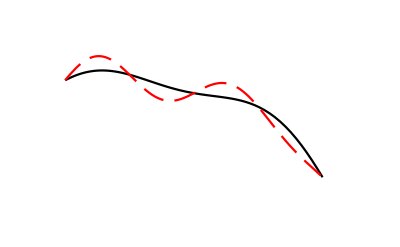

```mathematica
f=(-x+1) (Sin[2x]+x)/2;
g=f+0.5 Sin[4x];
Plot[{f,g},{x,0,π},PlotStyle->{Black,{Dashing[{0.04,0.02}],Red}},PlotRange->{{-.35,π+0.5},{-5,2}},Ticks->None,Axes->False]
```

思考：如果被积函数显含 β，形如： f(β,x,ẋ)，欧拉-拉格朗日定理会有什么变化？不变

会多出 k=0 对应于 β 的 一个方程吗？No， β 是参数，变分不出现 (∂f)/(∂β) 形式。参见§ 4.1.4 的推导

## § 4.4 坐标参数法

前几节的描述思路是，将高维空间的路线都表为参量 β 的参数方程：x_k(β)

线积分就表示为对参数的积分。

我们对参量 β 的要求是：在从起点到终点过程，它必须是单调的。

这一点容易理解，否则 ∫_β_1^β_2 …ⅆβ  就可能无法描述沿一条路线的积分。

——  因为这时参数方程中可能会出现多值函数。

在得到 Euler-Lagrange 方程之后，再确定如何选取 β。

—— 选取适当的 β，使得 Euler-Lagrange 方程尽量简单

前几节的例题，多选取 β 为从起点出发的弧长，

而 例 4.3.02 中我们甚至连 β 是什么都无需关注就求得球面上的短程线。

以上这种做法称为：一般参数法。

另一种做法，称为坐标参数法，

就是，从一开始就选取 N 维空间中的某个坐标本身为积分参数

其它坐标都用这个坐标的函数来表示

—— 相当于选取其中的一个坐标作为描述路线的参数方程的参量

——  当然这个坐标必须沿路线是单调的，比如可以选取时间 t

显然，坐标参数法可以看成是一般参数法的一种特殊情况，

但哈密顿原理通常用坐标参数法来表述，为便于今后的讨论，在此在稍作介绍。

现在的问题表述为：

由N个变量 x_k, k=1,2,…,N,构成的 N 维空间中给定起点 A 和终点 B

要确定从 A 到 B 的路线，使得沿这条路线的线积分

I=∫_(x_1^(A))^(x_1^(B)) g(x,x')ⅆ x_1     是个“极值”

\[FreakedSmiley]  这里稍作修正：严格意义上，积分未必是 extremum，可能是拐点

其中 x_1 是 N 个变量中的一个（不失一般性，设它为第一个），

在坐标参数法中，上标撇“ ′ ”代表对 x_1 求导 x'_k=(ⅆ x_k)/(ⅆ x_1)，比较  (ẋ)_k=(ⅆ x_k)/ⅆβ

用 x 表示 x_1,x_2,…,x_N， 而 x_[1]表示 x_2,x_3,…,x_N，下标 [1]表示排除 x_1

这时，线积分改写为： I=∫_(x_1^(A))^(x_1^(B)) g(x,x'_[1])ⅆ x_1，  下标 [1]表示排除 x'_1，因为 x'_1=(ⅆ x_1)/(ⅆ x_1)=1 ，不再是变量

显然，这个问题相当于 § 4.2 的 Euler-Lagrange 定理 中

{β=x_1
f=g   只不过有两点区别：{维数退化为 N-1 维
被积函数 f 中显含 β，比较 f(x,ẋ) 与 f(β,x_[1], x'_[1]) ，因为 β=x_1

这两点区别并不影响 § 4.2 中的 Euler-Lagrange 定理的成立。

因而，线积分 I 取极值的路线由以下 Euler-Lagrange 方程确定

ⅆ/(ⅆ x_1)((∂g(x,x'_[1]))/(∂x'_k))-(∂g(x,x'_[1]))/(∂x_k)=0，  k=2,3,…,N         无约束情况下的 Euler-Lagrange 方程

注意 Euler-Lagrange 方程是线积分“极值路线”的充要条件，这时

共有 N-1 个方程（N 个坐标有一个当成参量了）

路线的参数方程由 x_k=x_k(x_1) 描述，k=2,3,…,N，还有一个是 x_1=x_1

当然，x_1 必须是单调变化的。

类似地，对约束体系，当 C 个约束表示为以下形式时

G_a(x)=0

在坐标参数法中，线积分 I=∫_(x_1^(A))^(x_1^(B)) g(x,x'_[1])ⅆ x_1取“极值”的充要条件是路线满足

ⅆ/(ⅆ x_1)((∂g(x,x'_[1]))/(∂x'_k))-(∂g(x,x'_[1]))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)，     k=2,3,…,N

此为存在约束情况下的 Euler-Lagrange 方程

可以看到，一般参数法，对每一个坐标（k=1,2,…,N）都有一个 Euler-Lagrange 方程，

而 坐标参数法，似乎少了一个方程，因为 k=2,3,…,N。（其实有一个坐标的解直接给出了 x_1=x_1）

可以证明，如果我们定义

h=(∑_(k=2))^N x'_k(∂g(x,x'_[1]))/(∂x'_k)-g(x,x'_[1])      （这个形式让你想起什么？提示：设 x_1=t）广义能量函数

它满足以下所谓第二形式的 Euler-Lagrange 方程（下面会证明）

ⅆh/(ⅆ x_1)=-(∂g(x,x'_[1]))/(∂x_1)+(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)     （这个形式又让你想起什么？）

其中对无约束体系，或者消去受限坐标的约束体系，第二项（绿色项）等于 0。

##### 以下证明这个第二形式的 Euler-Lagrange 方程。

由定义：h=(∑_(k=2))^N x'_k(∂g(x,x'_[1]))/(∂x'_k)-g(x,x'_[1])   两边同时对 x_1 求导

ⅆh/(ⅆ x_1)=(∑_(k=2))^N ⅆ[x'_k(∂g(x,x'_[1]))/(∂x'_k)]/(ⅆ x_1)-(ⅆg(x,x'_[1]))/(ⅆ x_1)
=(∑_(k=2))^N [x''_k(∂g(x,x'_[1]))/(∂x'_k)+ x'_k(ⅆ (∂g(x,x'_[1])/∂x'_k))/(ⅆ x_1)]-(∂g(x,x'_[1]))/(∂x_1)-(∑_(k=2))^N(∂g(x,x'_[1]))/(∂x_k)x'_k-(∑_(k=2))^N(∂g(x,x'_[1]))/(ⅆ x'_k)x''_k
                   绿色项相消，紫色项利用 Euler-Lagrange 方程 (1.EquationNumbered)式 
=-(∂g(x,x'_[1]))/(∂x_1)-(∑_(k=2))^N x'_k(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)=-(∂g(x,x'_[1]))/(∂x_1)-(∑_(a=1))^C λ_a (∑_(k=2))^N (∂G_a(x))/(∂x_k)x'_k
=-(∂g(x,x'_[1]))/(∂x_1)-(∑_(a=1))^C λ_a  ((ⅆG_a(x))/(ⅆ x_1)-(∂G_a(x))/(∂x_1))        这里利用了  (ⅆG_a(x))/(ⅆ x_1)=(∂G_a(x))/(∂x_1)+(∑_(k=2))^N(∂G_a(x))/(∂x_k)x'_k
=-(∂g(x,x'_[1]))/(∂x_1)+(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)                                    这里利用了    (ⅆG_a(x))/(ⅆ x_1)=0

因此，还是可以找到 N 个方程：N-1 个 Euler-Lagrange 方程 和  1 个第二形式的 Euler-Lagrange 方程。

那么，这 N 个方程是否独立？（在力学中，广义功能定理与拉格朗日方程并不独立）

为此，我们来看看坐标参数法为何是一般参数法的一种特殊情况。

引入单调变化的参量 β，这时，

x_1=x_1(β),     x'_k=(ⅆ x_k)/(ⅆ x_1)=(ⅆ x_k/ⅆβ)/(ⅆ x_1/ⅆβ)=((ẋ)_k)/((ẋ)_1)，其中   (ẋ)_k≡(ⅆ x_k)/ⅆβ

再看线积分（记得 x 代表 x_1,x_2,…, x_N,  x'_[1] 代表 x'_2,x'_3,…,x'_N，其中 x'_k=(ⅆ x_k)/(ⅆ x_1) )

I=∫_(x_1^(A))^(x_1^(B)) g(x,x'_[1])ⅆ x_1 =∫_β_1^β_2 g(x,((ẋ)_[1])/((ẋ)_1))(ẋ)_1 ⅆβ =∫_β_1^β_2 f(x,ẋ)ⅆβ

所以，只需做如下变换，坐标参数法就化为一般参数法

f(x,ẋ)=(ẋ)_1 g(x,((ẋ)_[1])/((ẋ)_1))

线积分写成：I=∫_β_1^β_2 f(x,ẋ)ⅆβ    之后，

即可求 被积函数f(x,ẋ) 线积分 I 取极值的 N 个 Euler-Lagrange 方程。

对应于 x_k, k=1,2,…,N 共 N 个坐标，一般参数法的Euler-Lagrange 方程为

ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_k))-(∂f(x,ẋ))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)，  k=2,3,…,N

ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_1))-(∂f(x,ẋ))/(∂x_1)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)，  k=1     （其实与 k>1时的形式相同）

以下证明：

方程(1.EquationNumbered) 即为坐标参数法 中的N-1 个 Euler-Lagrange 方程

ⅆ/(ⅆ x_1)((∂g(x,x'_[1]))/(∂x'_k))-(∂g(x,x'_[1]))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x,t))/(∂x_k)

方程(1.EquationNumbered)即为坐标参数法中的那个所谓第二形式的 Euler-Lagrange 方程

ⅆh/(ⅆ x_1)=-(∂g(x,x'_[1]))/(∂x_1)-(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)，其中： h=(∑_(k=2))^N x'_k(∂g(x,x'_[1]))/(∂x'_k)-g(x,x'_[1])

先看一般参数法对应于 k>1 的 Euler-Lagrange 方程 (1.EquationNumbered)， 代入 f(x,ẋ)=(ẋ)_1 g(x,(ẋ)_[1]/(ẋ)_1)  可得

ⅆ/ⅆβ((∂[(ẋ)_1 g(x,(ẋ)_[1]/(ẋ)_1)])/(∂(ẋ)_k))-(∂[(ẋ)_1 g(x,(ẋ)_[1]/(ẋ)_1)])/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)       k=2,3,…, N

利用：    x'_k=ⅆ x_k/ⅆ x_1=(ẋ)_k/(ẋ)_1,      (ẋ)_k≡ⅆ x_k/ⅆβ

上式左=ⅆ/ⅆβ((ẋ)_1(∂[g(x,x'_[1])])/(∂(ẋ)_k))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_k)
=ⅆ/ⅆβ((ẋ)_1(∂[g(x,x'_[1])])/(∂x'_k)(∂x'_k)/(∂(ẋ)_k))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_k)           利用 x'_k=((ẋ)_k)/((ẋ)_1)  
=ⅆ/ⅆβ((ẋ)_1(∂[g(x,x'_[1])])/(∂x'_k)1/((ẋ)_1))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_k)
=ⅆ/ⅆβ((∂[g(x,x'_[1])])/(∂x'_k))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_k)

最后，令：β=x_1   ⟹  (ẋ)_1=ⅆ x_1/ⅆβ=1, 从而

ⅆ/(ⅆ x_1)((∂g(x,x'_[1]))/(∂x'_k))-(∂g(x,x'_[1]))/(∂x_k)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_k)，  k=2,3,…,N

对 k=2,3,…,N，一般参数法和坐标参数法得到的 Euler-Lagrange 方程一致。

再看一般参数法中 k=1的 Euler-Lagrange 方程 (1.EquationNumbered)：      ⅆ/ⅆβ((∂f(x,ẋ))/(∂(ẋ)_1))-(∂f(x,ẋ))/(∂x_1)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)

代入 f(x,ẋ)=(ẋ)_1 g(x,x'_[1])  可得 （记得： x'_k=ⅆ x_k/ⅆ x_1=(ⅆ x_k/ⅆβ)/(ⅆ x_1/ⅆβ)=(ẋ)_k/(ẋ)_1）

ⅆ/ⅆβ((∂[(ẋ)_1 g(x,x'_[1])])/(∂(ẋ)_1))-(∂[(ẋ)_1 g(x,x'_[1])])/(∂x_1)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)

上式左=ⅆ/ⅆβ(g(x,x'_[1])+(∑_(k=2))^N(ẋ)_1(∂[g(x,x'_[1])])/(∂x'_k)(∂x'_k)/(∂(ẋ)_1))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_1)       利用 x'_k=((ẋ)_k)/((ẋ)_1)
=ⅆ/ⅆβ(g(x,x'_[1])+(∑_(k=2))^N(ẋ)_1(∂[g(x,x'_[1])])/(∂x'_k)(-(ẋ)_k)/((ẋ)_1^2))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_1)
=-ⅆ/ⅆβ( (∑_(k=2))^N(∂[g(x,x'_[1])])/(∂x'_k)((ẋ)_k)/((ẋ)_1)-g(x,x'_[1]))-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_1)
=-ⅆ/ⅆβ[ (∑_(k=2))^N(∂[g(x,x'_[1])])/(∂x'_k)x'_k-g(x,x'_[1])]_(括号内即为 h)-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_1)
=-ⅆh/ⅆβ-(ẋ)_1(∂[g(x,x'_[1])])/(∂x_1)           注：h=(∑_(k=2))^N x'_k(∂g(x,x'_[1]))/(∂x'_k)-g(x,x'_[1])

最后，令：β=x_1   ⟹  (ẋ)_1=ⅆ x_1/ⅆβ=1, 从而

-ⅆh/(ⅆ x_1)-(∂[g(x,x'_[1])])/(∂x_1)=(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)

此即坐标参数法中的第二形式的 Euler-Lagrange 方程

ⅆh/(ⅆ x_1)=-(∂g(x,x'_[1]))/(∂x_1)-(∑_(a=1))^C λ_a(∂G_a(x))/(∂x_1)

有什么启发？

在力学应用中，如果把时间也当成一个广义坐标，用一般参数法写出的方程更为对称

而在坐标参数法中，需先写出 (N-1)个欧拉-拉格朗日方程，

再加上 1个第二形式的欧拉-拉格朗日方程，得到共  (N-1)+1 个方程

在一般参数法中，直接对各个坐标（包括作为广义坐标的时间）写出 N 个欧拉-拉格朗日方程

即可轻易囊括这所有的 N 个方程。

当然，这 N 个方程并不是独立的。在一般参数法中 ，这个性质源于 f(x,ẋ) 是 x 的齐一次函数。

##### 以下证明 f(x,ẋ)=(ẋ)_1 g(x,x'_[1]) 是 ẋ 的齐一次函数

f(x,ẋ)=(ẋ)_1 g(x,x'_[1])=(ẋ)_1 g(x,(ⅆ x_[1])/(ⅆ x_1))=(ẋ)_1 g(x,(ⅆ x_[1]/ⅆβ)/(ⅆ x_1/ⅆβ))=(ẋ)_1 g(x,((ẋ)_[1])/((ẋ)_1))

⟹    f(x,λ ẋ)=λ(ẋ)_1 g(x,(λ(ẋ)_[1])/(λ(ẋ)_1))=λ(ẋ)_1 g(x,x'_[1])=λ f(x,ẋ)      即： f(x,λ ẋ)=λ f(x,ẋ)

故：f(x,ẋ) 是 (ẋ)_k, (k=1,2,…,N) 的齐一次函数。 (ẋ)_1=(ⅆ x_1)/ⅆβ=1≠0，第一个方程不独立与其它 E-L 方程。

注意这里 N=D+1， 其中 D 为位形空间维度，而 1 来自时间

数学上，一般参数法似乎仅仅是形式上更为对称，然而，若赋予物理内涵，就可对应于相对论形式。

### § 4.5.0 哈密顿原理

作用量积分：

I=I(δa,[q],[η])=∫_β_1^β_2 L(q,q̇,β)ⅆβ      这里顶标上的一点是对参量 β 求导

哈密顿原理要求运动路线是作用量积分取驻值，即：I=I(δa,[q],[η])=∫_t_1^t_2 L(q,q̇,β)ⅆβ 取驻值。

而变分原理告诉我们，线积分（作用量积分）I 取驻值的充要条件是 Euler-Lagrange 方程

ⅆ/ⅆβ((∂L (q,q̇,β))/(∂(q̇)_k))-(∂L (q,q̇,β))/(∂q_k)=0,       k=1,2,…, D

以上是对无约束体系。

对约束体系，相应的，哈密顿原理变成：

作用量积分 I(δa,[q],[η])=∫_β_1^β_2 L (q,q̇,β)ⅆβ  在线积分两端点确定的条件下并且

在约束条件 G_a(q,β)=0,  a=1,2,…,C  下取驻值（即：一阶变分 δ I=0）

的充要条件是：积分路线 q_k(β) 满足类约束体系的拉格朗日方程

ⅆ/ⅆβ((∂L (q,q̇,β))/(∂(q̇)_k))-(∂L (q,q̇,β))/(∂q_k)=(∑_(a=1))^C λ_a (∂G_a(q,β))/(∂q_k),       k=1,2,…, D

这 D 个方程可以和 C 个约束方程联立求解 q_k(β) 和  λ_a 共 D+C 个变量。

注意这里的欧拉-拉格朗日方程只保证作用量积分取驻值，并不能保证其解一定是力学体系的解，

只有在力学体系满足“零虚功全保守”条件下，两者才达成驻值充要条件的方程与力学运动方程的一致。